# Ejercicio I.3: Simulación de elementos de la red

## Nombre del Alumno: Felix Sanz González DNI: 78997168B

# -Graphics-

# 1.- Generacion de paquetes, y transmisiones. Abstracción de un enlace

```mathematica
Clear["Global`*"]
err = 0.1;
npaquetes = 1000;
lambda = 2000;
a = 2;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
```

1/6000

1066.67

```mathematica
RndExp[ratio_] := -Log[RandomReal[]]/ratio//N;
```

```mathematica
RndExp[lambda]
```

0.00062201

```mathematica
GetArrivals[transmisionlista_,tp_]:=Map[(If[#[[4]]==0,#[[1]]+#[[2]]+tp,Unevaluated[Sequence[]]])&,transmisionlista];
```

```mathematica
(*Source[tentrellegadas_,len_,idFlow_,period_,idIn_:0]:=*)
createPackets[lambda_,len_,idFlow_,period_,idIn_]:= 
Module[{checktime =0, n =1, lista = {idIn}},
NestWhileList[({checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime})&, 
{checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime}, (#[[1]]< period)&]];
```

```mathematica
paquetes = createPackets[lambda,l,1,1,0];
paquetes[[1;;5]]
Last[paquetes]
```

{{0.000201737,64.52,1,0,0,1,1,{0},0.000201737},{0.000464857,206.025,2,0,0,2,1,{0},0.000464857},{0.000877013,1239.75,3,0,0,3,1,{0},0.000877013},{0.00200753,526.061,4,0,0,4,1,{0},0.00200753},{0.00351246,487.107,5,0,0,5,1,{0},0.00351246}}

{1.00004,431.636,1990,0,0,1990,1,{0},1.00004}

```mathematica
(* pkt={chkTime,length,nseqLink,error,nrtx,nseqFlow,flowId,{path},{timePath}} *)

createTx[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
None;
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]

createTxSW[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
];

createTxGBN[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c);n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]
```

```mathematica
paquetesNormales = createTx[paquetes,p,TpSW,c];
```

```mathematica
paquetesNormales⟦1;;5⟧
```

{{0.000614983,727.014,1,0,0,1,1,{0},0.000614983},{0.00117551,665.791,2,0,0,2,1,{0},0.000616127},{0.0017169,169.931,3,0,0,3,1,{0},0.00127791},{0.00210334,624.169,4,0,0,4,1,{0},0.00129157},{0.00263172,1147.81,5,0,0,5,1,{0},0.00168539}}

```mathematica
paquetesSW = createTxSW[paquetes,p,TpSW,c];
paquetesSW[[1;;5]]
```

{{0.000614983,727.014,1,1,0,1,1,{0},0.000614983},{0.00117551,727.014,1,0,1,1,1,{0},0.000614983},{0.00173603,665.791,2,0,0,2,1,{0},0.000616127},{0.00227743,169.931,3,0,0,3,1,{0},0.00127791},{0.00266386,624.169,4,0,0,4,1,{0},0.00129157}}

```mathematica
paquetesGBN = createTxGBN[paquetes,p,TpSW,c];
paquetesGBN[[1;;5]]
```

{{0.000614983,727.014,1,0,0,1,1,{0},0.000614983},{0.000842175,665.791,2,1,0,2,1,{0},0.000616127},{0.00138357,665.791,2,0,1,2,1,{0},0.000616127},{0.00159163,169.931,3,1,0,3,1,{0},0.00127791},{0.00197806,169.931,3,1,1,3,1,{0},0.00127791}}

```mathematica
Get["C:\\Users\\felix\\Desktop\\Todo\\U.P.V\\MASTER\\Segundo\\Asignaturas\\Rendimiento en Redes de Telecomunicacion\\Casos\\Caso I\\drawTxPRM2024.m"];
```

```mathematica
?drawTxPRM2024`*
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesNormales]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesSW]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.005 en WW*)
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesGBN]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.004 en WW*)
```

```mathematica
(*Tenemos que conseguir hacer una lista de paquetes que no contenga los paquetes erroneos --> Filtrar *)
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

```mathematica
paquetesbuenosNormales = filtrarPaquetes[paquetesNormales,c,TpSW];
paquetesNormales[[1;;20]]
paquetesbuenosNormales[[1;;20]]
paquetesbuenosSW = filtrarPaquetes[paquetesSW,c,TpSW];
paquetesSW[[1;;20]]
paquetesbuenosSW[[1;;20]]
paquetesbuenosGBN = filtrarPaquetes[paquetesGBN,c,TpSW];
paquetesGBN[[1;;20]]
paquetesbuenosGBN[[1;;10]]
```

{{0.000614983,727.014,1,0,0,1,1,{0},0.000614983},{0.00117551,665.791,2,0,0,2,1,{0},0.000616127},{0.0017169,169.931,3,0,0,3,1,{0},0.00127791},{0.00210334,624.169,4,0,0,4,1,{0},0.00129157},{0.00263172,1147.81,5,0,0,5,1,{0},0.00168539},{0.00332375,1312.21,6,0,0,6,1,{0},0.00238605},{0.00406715,2802.14,7,0,0,7,1,{0},0.00327473},{0.00527615,1200.18,8,0,0,8,1,{0},0.00398246},{0.00598454,1453.72,9,0,0,9,1,{0},0.00398763},{0.00677216,32.2569,10,0,0,10,1,{0},0.00402216},{0.00711557,403.563,11,0,0,11,1,{0},0.00445587},{0.00757502,1990.34,12,0,0,12,1,{0},0.00472991},{0.00853033,426.626,13,0,0,13,1,{0},0.0052622},{0.00899699,229.73,14,0,0,14,1,{0},0.0053225},{0.00940211,1313.63,15,0,0,15,1,{0},0.00542286},{0.010146,2510.35,16,0,0,16,1,{0},0.00552372},{0.0112638,1964.61,17,0,0,17,1,{0},0.00557784},{0.012211,522.109,18,0,0,18,1,{0},0.00564563},{0.0127075,1421.06,19,0,0,19,1,{0},0.00589779},{0.013485,1458.66,20,0,0,20,1,{0},0.00609587}}

{{0.00100884,727.014,1,0,0,1,1,{0},0.000614983},{0.00155023,665.791,2,0,0,2,1,{0},0.000616127},{0.00193667,169.931,3,0,0,3,1,{0},0.00127791},{0.00246506,624.169,4,0,0,4,1,{0},0.00129157},{0.00315708,1147.81,5,0,0,5,1,{0},0.00168539},{0.00390048,1312.21,6,0,0,6,1,{0},0.00238605},{0.00510948,2802.14,7,0,0,7,1,{0},0.00327473},{0.00581787,1200.18,8,0,0,8,1,{0},0.00398246},{0.00660549,1453.72,9,0,0,9,1,{0},0.00398763},{0.00694891,32.2569,10,0,0,10,1,{0},0.00402216},{0.00740835,403.563,11,0,0,11,1,{0},0.00445587},{0.00836367,1990.34,12,0,0,12,1,{0},0.00472991},{0.00883032,426.626,13,0,0,13,1,{0},0.0052622},{0.00923544,229.73,14,0,0,14,1,{0},0.0053225},{0.00997929,1313.63,15,0,0,15,1,{0},0.00542286},{0.0110971,2510.35,16,0,0,16,1,{0},0.00552372},{0.0120444,1964.61,17,0,0,17,1,{0},0.00557784},{0.0125409,522.109,18,0,0,18,1,{0},0.00564563},{0.0133183,1421.06,19,0,0,19,1,{0},0.00589779},{0.0141075,1458.66,20,0,0,20,1,{0},0.00609587}}

{{0.000614983,727.014,1,1,0,1,1,{0},0.000614983},{0.00117551,727.014,1,0,1,1,1,{0},0.000614983},{0.00173603,665.791,2,0,0,2,1,{0},0.000616127},{0.00227743,169.931,3,0,0,3,1,{0},0.00127791},{0.00266386,624.169,4,0,0,4,1,{0},0.00129157},{0.00319225,1147.81,5,0,0,5,1,{0},0.00168539},{0.00388427,1312.21,6,0,0,6,1,{0},0.00238605},{0.00462767,2802.14,7,1,0,7,1,{0},0.00327473},{0.00583667,2802.14,7,0,1,7,1,{0},0.00327473},{0.00704567,1200.18,8,0,0,8,1,{0},0.00398246},{0.00775406,1453.72,9,0,0,9,1,{0},0.00398763},{0.00854168,32.2569,10,0,0,10,1,{0},0.00402216},{0.0088851,403.563,11,0,0,11,1,{0},0.00445587},{0.00934454,1990.34,12,0,0,12,1,{0},0.00472991},{0.0102999,426.626,13,0,0,13,1,{0},0.0052622},{0.0107665,229.73,14,0,0,14,1,{0},0.0053225},{0.0111716,1313.63,15,0,0,15,1,{0},0.00542286},{0.0119155,2510.35,16,0,0,16,1,{0},0.00552372},{0.0130333,1964.61,17,0,0,17,1,{0},0.00557784},{0.0139806,522.109,18,0,0,18,1,{0},0.00564563}}

{{0.00156937,727.014,1,0,1,1,1,{0},0.000614983},{0.00211076,665.791,2,0,0,2,1,{0},0.000616127},{0.0024972,169.931,3,0,0,3,1,{0},0.00127791},{0.00302558,624.169,4,0,0,4,1,{0},0.00129157},{0.00371761,1147.81,5,0,0,5,1,{0},0.00168539},{0.00446101,1312.21,6,0,0,6,1,{0},0.00238605},{0.00687901,2802.14,7,0,1,7,1,{0},0.00327473},{0.0075874,1200.18,8,0,0,8,1,{0},0.00398246},{0.00837502,1453.72,9,0,0,9,1,{0},0.00398763},{0.00871843,32.2569,10,0,0,10,1,{0},0.00402216},{0.00917788,403.563,11,0,0,11,1,{0},0.00445587},{0.0101332,1990.34,12,0,0,12,1,{0},0.00472991},{0.0105998,426.626,13,0,0,13,1,{0},0.0052622},{0.011005,229.73,14,0,0,14,1,{0},0.0053225},{0.0117488,1313.63,15,0,0,15,1,{0},0.00542286},{0.0128666,2510.35,16,0,0,16,1,{0},0.00552372},{0.0138139,1964.61,17,0,0,17,1,{0},0.00557784},{0.0143104,522.109,18,0,0,18,1,{0},0.00564563},{0.0150878,1421.06,19,0,0,19,1,{0},0.00589779},{0.015877,1458.66,20,0,0,20,1,{0},0.00609587}}

{{0.000614983,727.014,1,0,0,1,1,{0},0.000614983},{0.000842175,665.791,2,1,0,2,1,{0},0.000616127},{0.00138357,665.791,2,0,1,2,1,{0},0.000616127},{0.00159163,169.931,3,1,0,3,1,{0},0.00127791},{0.00197806,169.931,3,1,1,3,1,{0},0.00127791},{0.0023645,169.931,3,0,2,3,1,{0},0.00127791},{0.0024176,624.169,4,0,0,4,1,{0},0.00129157},{0.00261266,1147.81,5,0,0,5,1,{0},0.00168539},{0.00297135,1312.21,6,0,0,6,1,{0},0.00238605},{0.00338141,2802.14,7,0,0,7,1,{0},0.00327473},{0.00425708,1200.18,8,0,0,8,1,{0},0.00398246},{0.00463214,1453.72,9,0,0,9,1,{0},0.00398763},{0.00508642,32.2569,10,0,0,10,1,{0},0.00402216},{0.00509651,403.563,11,0,0,11,1,{0},0.00445587},{0.00522262,1990.34,12,0,0,12,1,{0},0.00472991},{0.0058446,426.626,13,0,0,13,1,{0},0.0052622},{0.00597792,229.73,14,0,0,14,1,{0},0.0053225},{0.00604971,1313.63,15,0,0,15,1,{0},0.00542286},{0.00646022,2510.35,16,0,0,16,1,{0},0.00552372},{0.00724471,1964.61,17,0,0,17,1,{0},0.00557784}}

{{0.00100884,727.014,1,0,0,1,1,{0},0.000614983},{0.00175829,665.791,2,0,1,2,1,{0},0.000616127},{0.00258427,169.931,3,0,2,3,1,{0},0.00127791},{0.00277932,624.169,4,0,0,4,1,{0},0.00129157},{0.00313801,1147.81,5,0,0,5,1,{0},0.00168539},{0.00354808,1312.21,6,0,0,6,1,{0},0.00238605},{0.00442375,2802.14,7,0,0,7,1,{0},0.00327473},{0.0047988,1200.18,8,0,0,8,1,{0},0.00398246},{0.00525309,1453.72,9,0,0,9,1,{0},0.00398763},{0.00526317,32.2569,10,0,0,10,1,{0},0.00402216}}

# 2 y 3.- Abstracción de un nodo de conmutación. Funciones de filtrado y multiplexado de paquetes.

Debemos implementar una función que nos permita eliminar los paquetes que contienen error, segun el campo de paquete que indica si es un paquete con error

```mathematica
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

Debemos implementar una función que nos permita dividir y conmutar  el trafico entrante a un nodo por sus distintos enlaces de salida. 
Está función tiene como parámetros de entrada la lista de paquetes, las probabilidades de los enlaces de salida y los enlaces de salida

```mathematica
(*Esta funcion da error y NO SE USA*)
Node1[in_,probs_]:=Module[{cumulativeProbs,outcomes,nProbs,nGroups,r,assignedGroups},(*Verificar que las probabilidades sumen 1*)If[Total[probs]!=1,Return["Error: La suma de las probabilidades debe ser 1."]];
(*Calcular los límites acumulados de las probabilidades*)
cumulativeProbs=Accumulate[probs];
(*Número de probabilidades y número de grupos*)
nProbs=Length[probs];
nGroups=nProbs;
(*Asignar cada elemento de'in' a un grupo según probabilidades acumuladas*)
assignedGroups=Map[With[{r=RandomReal[]},FirstPosition[cumulativeProbs,_?(#>=r&)][[1]],in];
(*Mostrar valores aleatorios y asignaciones para depuración*)
Print["Valores aleatorios: ",r,Length[in]]];
Print["Grupos asignados: ",assignedGroups];
(*Crear la lista de resultados agrupados*)
outcomes=Table[Select[Transpose[{in,assignedGroups}],#[[2]]==i+1&][[All,1]],{i,1,Length[probs]}];
(*Devolver los resultados agrupados por etiquetas*)
outcomes]
```

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId} *)
(*Esta es la función que se usa*)

Node2[in_,prob_]:=Reap[
Map[If[RandomReal[]<prob,Sow[#,1],Sow[#,2]]&,in],
_,#2&][[2]];
```

Debemos implementar una función que nos permita multiplexar el trafico entrante a un nodo, para asi obtener una unica lista, ordenada segun el instante de llegada de cada paquete.

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId,{path} *)
Multiplexar[in_,idNodo_]:=Module[{aux={},aux2={},nodes={},times={}},
aux=Flatten[in,1]; (*Concatenar listas de paquetes en una sola lista*)
aux=SortBy[aux,#[[1]]&]; (*Ordenar la nueva lista en base al tiempo en el que han llegado los paquetes al nodo*)
Map[{

nodes=#[[8]];(*Extraer los nodos por los que ha pasado el paquete actual*)
AppendTo[nodes,idNodo]; (*Agregar el nodo actual a la lista de nodos por los que ha pasado el paquete actual*)

AppendTo[aux2,{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],nodes,#[[9]]}]}&,aux]; (*Crea la nueva lista de paquetes*)
	aux2
];
```

```mathematica
{enlace1,enlace2}= Node2[paquetesbuenosNormales[[1;;15]],0.5];
Flatten[{enlace1,enlace2},1]
enlace1
enlace2
```

{{0.00100884,727.014,1,0,0,1,1,{0},0.000614983},{0.00155023,665.791,2,0,0,2,1,{0},0.000616127},{0.00193667,169.931,3,0,0,3,1,{0},0.00127791},{0.00510948,2802.14,7,0,0,7,1,{0},0.00327473},{0.00581787,1200.18,8,0,0,8,1,{0},0.00398246},{0.00836367,1990.34,12,0,0,12,1,{0},0.00472991},{0.00246506,624.169,4,0,0,4,1,{0},0.00129157},{0.00315708,1147.81,5,0,0,5,1,{0},0.00168539},{0.00390048,1312.21,6,0,0,6,1,{0},0.00238605},{0.00660549,1453.72,9,0,0,9,1,{0},0.00398763},{0.00694891,32.2569,10,0,0,10,1,{0},0.00402216},{0.00740835,403.563,11,0,0,11,1,{0},0.00445587},{0.00883032,426.626,13,0,0,13,1,{0},0.0052622},{0.00923544,229.73,14,0,0,14,1,{0},0.0053225},{0.00997929,1313.63,15,0,0,15,1,{0},0.00542286}}

{{0.00100884,727.014,1,0,0,1,1,{0},0.000614983},{0.00155023,665.791,2,0,0,2,1,{0},0.000616127},{0.00193667,169.931,3,0,0,3,1,{0},0.00127791},{0.00510948,2802.14,7,0,0,7,1,{0},0.00327473},{0.00581787,1200.18,8,0,0,8,1,{0},0.00398246},{0.00836367,1990.34,12,0,0,12,1,{0},0.00472991}}

{{0.00246506,624.169,4,0,0,4,1,{0},0.00129157},{0.00315708,1147.81,5,0,0,5,1,{0},0.00168539},{0.00390048,1312.21,6,0,0,6,1,{0},0.00238605},{0.00660549,1453.72,9,0,0,9,1,{0},0.00398763},{0.00694891,32.2569,10,0,0,10,1,{0},0.00402216},{0.00740835,403.563,11,0,0,11,1,{0},0.00445587},{0.00883032,426.626,13,0,0,13,1,{0},0.0052622},{0.00923544,229.73,14,0,0,14,1,{0},0.0053225},{0.00997929,1313.63,15,0,0,15,1,{0},0.00542286}}

```mathematica
in2 = Multiplexar[{enlace1,enlace2},A]
```

{{0.00100884,727.014,1,0,0,1,1,{0,A},0.000614983},{0.00155023,665.791,2,0,0,2,1,{0,A},0.000616127},{0.00193667,169.931,3,0,0,3,1,{0,A},0.00127791},{0.00246506,624.169,4,0,0,4,1,{0,A},0.00129157},{0.00315708,1147.81,5,0,0,5,1,{0,A},0.00168539},{0.00390048,1312.21,6,0,0,6,1,{0,A},0.00238605},{0.00510948,2802.14,7,0,0,7,1,{0,A},0.00327473},{0.00581787,1200.18,8,0,0,8,1,{0,A},0.00398246},{0.00660549,1453.72,9,0,0,9,1,{0,A},0.00398763},{0.00694891,32.2569,10,0,0,10,1,{0,A},0.00402216},{0.00740835,403.563,11,0,0,11,1,{0,A},0.00445587},{0.00836367,1990.34,12,0,0,12,1,{0,A},0.00472991},{0.00883032,426.626,13,0,0,13,1,{0,A},0.0052622},{0.00923544,229.73,14,0,0,14,1,{0,A},0.0053225},{0.00997929,1313.63,15,0,0,15,1,{0,A},0.00542286}}

```mathematica
(*Esta funcion permite añadir numeros de secuencia a los paquetes de un flujo, es decir, a los paquetes que ya se sabe que van por un enlace*)
añadirNumSec[lista_,max_]:=Table[Append[lista[[i]],Mod[i-1,max]],{i,1,Length[lista]}]
```

```mathematica
añadirNumSec[enlace1,4]
```

{{0.00100884,727.014,1,0,0,1,1,{0},0.000614983,0},{0.00155023,665.791,2,0,0,2,1,{0},0.000616127,1},{0.00193667,169.931,3,0,0,3,1,{0},0.00127791,2},{0.00510948,2802.14,7,0,0,7,1,{0},0.00327473,3},{0.00581787,1200.18,8,0,0,8,1,{0},0.00398246,0},{0.00836367,1990.34,12,0,0,12,1,{0},0.00472991,1}}

# 4A.- Simulación de transmisión de paquetes en la topología de red SIN protocolo

```mathematica
SetAttributes[createPrimitive,HoldAll];
MakeBoxes[Interpretation[expr,p]]//DisplayForm;
InterpretationBox["expr",p]//DisplayForm;
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]];

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
arrow=Graphics[face[0.01]];
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

-Graphics-

```mathematica
err = 0.1;
npaquetes = 250;
lambda = 2000;
a = 2;
period = 1;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
prob1 = 1/4;
prob2 = 1/3;
prob5 = 1/2;
```

1/6000

1066.67

```mathematica
in1 = createPackets[lambda,l,1,period,"Ori-1"];
Last[in1]
in5 = createPackets[lambda,l,1,period,"Ori-5"];
Last[in5]
in2 = createPackets[lambda,l,1,period,"Ori-2"];
Last[in2]
in1[[1;;15]];
totalin = Length[in1]+Length[in5]+Length[in2]
```

{1.0015,5530.91,2129,0,0,2129,1,{Ori-1},1.0015}

{1.0003,411.618,1949,0,0,1949,1,{Ori-5},1.0003}

{1.00011,50.999,1982,0,0,1982,1,{Ori-2},1.00011}

6060

```mathematica
{paquetes12,paquetes15} =Node2[in1,prob1];

paquetes12[[1;;15]]
paquetes15[[1;;15]]
Length[paquetes12];
Length[paquetes15];
Length[paquetes12]/(Length[paquetes15]+Length[paquetes12])//N
```

{{0.000318547,51.5933,1,0,0,1,1,{Ori-1},0.000318547},{0.000601746,1491.71,2,0,0,2,1,{Ori-1},0.000601746},{0.00185216,1015.22,4,0,0,4,1,{Ori-1},0.00185216},{0.00200921,2219.06,5,0,0,5,1,{Ori-1},0.00200921},{0.00230502,458.999,6,0,0,6,1,{Ori-1},0.00230502},{0.00247192,743.368,7,0,0,7,1,{Ori-1},0.00247192},{0.00318144,589.403,8,0,0,8,1,{Ori-1},0.00318144},{0.00397859,74.0335,9,0,0,9,1,{Ori-1},0.00397859},{0.00407352,444.86,11,0,0,11,1,{Ori-1},0.00407352},{0.00718156,2273.4,15,0,0,15,1,{Ori-1},0.00718156},{0.00753403,1912.32,16,0,0,16,1,{Ori-1},0.00753403},{0.00777422,1371.25,17,0,0,17,1,{Ori-1},0.00777422},{0.00880597,4230.8,19,0,0,19,1,{Ori-1},0.00880597},{0.00958785,536.94,20,0,0,20,1,{Ori-1},0.00958785},{0.00962073,76.4908,21,0,0,21,1,{Ori-1},0.00962073}}

{{0.00163113,125.491,3,0,0,3,1,{Ori-1},0.00163113},{0.00398149,1560.33,10,0,0,10,1,{Ori-1},0.00398149},{0.00417901,202.07,12,0,0,12,1,{Ori-1},0.00417901},{0.00618393,210.585,13,0,0,13,1,{Ori-1},0.00618393},{0.00666749,803.938,14,0,0,14,1,{Ori-1},0.00666749},{0.00841019,3793.28,18,0,0,18,1,{Ori-1},0.00841019},{0.0103668,49.7821,23,0,0,23,1,{Ori-1},0.0103668},{0.0110667,317.551,24,0,0,24,1,{Ori-1},0.0110667},{0.0172083,167.505,28,0,0,28,1,{Ori-1},0.0172083},{0.0186173,2863.91,32,0,0,32,1,{Ori-1},0.0186173},{0.0259785,1996.6,41,0,0,41,1,{Ori-1},0.0259785},{0.0268886,1407.65,42,0,0,42,1,{Ori-1},0.0268886},{0.027871,319.634,44,0,0,44,1,{Ori-1},0.027871},{0.0294052,2420.16,47,0,0,47,1,{Ori-1},0.0294052},{0.0389849,12.9077,60,0,0,60,1,{Ori-1},0.0389849}}

0.743871

```mathematica
tx12 = createTx[paquetes12,p,TpSW,c];
tx15 = createTx[paquetes15,p,TpSW,c];
```

```mathematica
tx15[[1;;10]]
in5[[1;;10]]

inOKtx15 = filtrarPaquetes[tx15,c,TpSW];

intotal5= Multiplexar[{in5,inOKtx15},5];
intotal5[[1;;10]]

{paquetes52,paquetes54} = Node2[intotal5,prob5];
tx52 = createTx[paquetes52,p,TpSW,c];
tx54 = createTx[paquetes54,p,TpSW,c];
```

{{0.00163113,125.491,1,0,0,3,1,{Ori-1},0.00163113},{0.00398149,1560.33,2,0,0,10,1,{Ori-1},0.00398149},{0.00480243,202.07,3,0,0,12,1,{Ori-1},0.00417901},{0.00618393,210.585,4,0,0,13,1,{Ori-1},0.00618393},{0.00666749,803.938,5,0,0,14,1,{Ori-1},0.00666749},{0.00841019,3793.28,6,0,0,18,1,{Ori-1},0.00841019},{0.0103668,49.7821,7,0,0,23,1,{Ori-1},0.0103668},{0.0110667,317.551,8,0,0,24,1,{Ori-1},0.0110667},{0.0172083,167.505,9,0,0,28,1,{Ori-1},0.0172083},{0.0186173,2863.91,10,0,0,32,1,{Ori-1},0.0186173}}

{{0.0011197,1830.63,1,0,0,1,1,{Ori-5},0.0011197},{0.00164054,1114.77,2,0,0,2,1,{Ori-5},0.00164054},{0.00214843,1826.74,3,0,0,3,1,{Ori-5},0.00214843},{0.00239396,535.586,4,0,0,4,1,{Ori-5},0.00239396},{0.00333221,116.663,5,0,0,5,1,{Ori-5},0.00333221},{0.0038614,953.575,6,0,0,6,1,{Ori-5},0.0038614},{0.0051449,2235.51,7,0,0,7,1,{Ori-5},0.0051449},{0.00574281,2112.52,8,0,0,8,1,{Ori-5},0.00574281},{0.00608457,6797.52,9,0,0,9,1,{Ori-5},0.00608457},{0.00697325,1032.62,10,0,0,10,1,{Ori-5},0.00697325}}

{{0.0011197,1830.63,1,0,0,1,1,{Ori-5,5},0.0011197},{0.00164054,1114.77,2,0,0,2,1,{Ori-5,5},0.00164054},{0.00183702,125.491,1,0,0,3,1,{Ori-1,5},0.00163113},{0.00214843,1826.74,3,0,0,3,1,{Ori-5,5},0.00214843},{0.00239396,535.586,4,0,0,4,1,{Ori-5,5},0.00239396},{0.00333221,116.663,5,0,0,5,1,{Ori-5,5},0.00333221},{0.0038614,953.575,6,0,0,6,1,{Ori-5,5},0.0038614},{0.00463576,1560.33,2,0,0,10,1,{Ori-1,5},0.00398149},{0.00503224,202.07,3,0,0,12,1,{Ori-1,5},0.00417901},{0.0051449,2235.51,7,0,0,7,1,{Ori-5,5},0.0051449}}

```mathematica
inOKtx12 = filtrarPaquetes[tx12,c,TpSW];
inOKtx52 = filtrarPaquetes[tx52,c,TpSW];
intotal2 = Multiplexar[{in2,inOKtx52, inOKtx12},2];
in2[[1;;10]]
inOKtx52[[1;;10]]
inOKtx12[[1;;10]]
intotal2[[1;;10]]
```

{{0.000550137,8531.09,1,0,0,1,1,{Ori-2},0.000550137},{0.000609285,206.487,2,0,0,2,1,{Ori-2},0.000609285},{0.00306459,107.5,3,0,0,3,1,{Ori-2},0.00306459},{0.00340717,1007.46,4,0,0,4,1,{Ori-2},0.00340717},{0.00395449,2317.48,5,0,0,5,1,{Ori-2},0.00395449},{0.00419942,630.786,6,0,0,6,1,{Ori-2},0.00419942},{0.00441063,652.607,7,0,0,7,1,{Ori-2},0.00441063},{0.00557067,639.244,8,0,0,8,1,{Ori-2},0.00557067},{0.0056941,485.842,9,0,0,9,1,{Ori-2},0.0056941},{0.00587442,3056.69,10,0,0,10,1,{Ori-2},0.00587442}}

{{0.00185844,1830.63,1,0,0,1,1,{Ori-5,5},0.0011197},{0.00254014,1114.77,2,0,0,2,1,{Ori-5,5},0.00164054},{0.00291269,125.491,3,0,0,3,1,{Ori-1,5},0.00163113},{0.00381688,1826.74,4,0,0,3,1,{Ori-5,5},0.00214843},{0.00431758,535.586,5,0,0,4,1,{Ori-5,5},0.00239396},{0.00468737,116.663,6,0,0,5,1,{Ori-5,5},0.00333221},{0.0053187,953.575,7,0,0,6,1,{Ori-5,5},0.0038614},{0.00571518,202.07,8,0,0,12,1,{Ori-1,5},0.00417901},{0.00674711,2235.51,9,0,0,7,1,{Ori-5,5},0.0051449},{0.00920467,6797.52,10,0,0,9,1,{Ori-5,5},0.00608457}}

{{0.000501336,51.5933,1,0,0,1,1,{Ori-1},0.000318547},{0.00130083,1491.71,2,0,0,2,1,{Ori-1},0.000601746},{0.00233608,1015.22,3,0,0,4,1,{Ori-1},0.00185216},{0.00336287,2219.06,4,0,0,5,1,{Ori-1},0.00200921},{0.00383964,458.999,5,0,0,6,1,{Ori-1},0.00230502},{0.00440528,743.368,6,0,0,7,1,{Ori-1},0.00247192},{0.0049228,589.403,7,0,0,8,1,{Ori-1},0.00318144},{0.00527927,74.0335,8,0,0,9,1,{Ori-1},0.00397859},{0.00575162,444.86,9,0,0,11,1,{Ori-1},0.00407352},{0.00805866,2273.4,10,0,0,15,1,{Ori-1},0.00718156}}

{{0.000501336,51.5933,1,0,0,1,1,{Ori-1,2},0.000318547},{0.000550137,8531.09,1,0,0,1,1,{Ori-2,2},0.000550137},{0.000609285,206.487,2,0,0,2,1,{Ori-2,2},0.000609285},{0.00130083,1491.71,2,0,0,2,1,{Ori-1,2},0.000601746},{0.00185844,1830.63,1,0,0,1,1,{Ori-5,5,2},0.0011197},{0.00233608,1015.22,3,0,0,4,1,{Ori-1,2},0.00185216},{0.00254014,1114.77,2,0,0,2,1,{Ori-5,5,2},0.00164054},{0.00291269,125.491,3,0,0,3,1,{Ori-1,5,2},0.00163113},{0.00306459,107.5,3,0,0,3,1,{Ori-2,2},0.00306459},{0.00336287,2219.06,4,0,0,5,1,{Ori-1,2},0.00200921}}

```mathematica
{paquetes23,paquetes24} = Node2[intotal2,prob2];

tx23 = createTx[paquetes23,p,TpSW,c];
tx24 = createTx[paquetes24,p,TpSW,c];
```

```mathematica
inOK3 = filtrarPaquetes[tx23,c,TpSW];
out3 = Multiplexar[{inOK3},3];
out3[[1;;10]]
```

{{0.000684126,51.5933,1,0,0,1,1,{Ori-1,2,3},0.000318547},{0.00368342,8531.09,2,0,0,1,1,{Ori-2,2,3},0.000550137},{0.00408128,206.487,3,0,0,2,1,{Ori-2,2,3},0.000609285},{0.00498669,1830.63,4,0,0,1,1,{Ori-5,5,2,3},0.0011197},{0.00563728,1015.22,5,0,0,4,1,{Ori-1,2,3},0.00185216},{0.00631898,1114.77,6,0,0,2,1,{Ori-5,5,2,3},0.00164054},{0.0066859,107.5,7,0,0,3,1,{Ori-2,2,3},0.00306459},{0.00733407,1007.46,8,0,0,4,1,{Ori-2,2,3},0.00340717},{0.00839161,2317.48,9,0,0,5,1,{Ori-2,2,3},0.00395449},{0.00892207,630.786,10,0,0,6,1,{Ori-2,2,3},0.00419942}}

```mathematica
inOKtx54 = filtrarPaquetes[tx54,c,TpSW];
inOKtx24 = filtrarPaquetes[tx24,c,TpSW];
intotal4 = Multiplexar[{inOKtx54, inOKtx24},4];
inOKtx54[[1;;10]]
inOKtx24[[1;;10]]
intotal4[[1;;10]]
```

{{0.00529003,1560.33,1,0,0,10,1,{Ori-1,5},0.00398149},{0.00656964,2112.52,2,0,0,8,1,{Ori-5,5},0.00574281},{0.0074626,1032.62,3,0,0,10,1,{Ori-5,5},0.00697325},{0.00804717,803.938,4,0,0,14,1,{Ori-1,5},0.00666749},{0.0086506,864.322,5,0,0,12,1,{Ori-5,5},0.00804006},{0.0120999,2188.02,6,0,0,16,1,{Ori-5,5},0.0112495},{0.0128733,368.105,7,0,0,18,1,{Ori-5,5},0.0125916},{0.0167371,53.9048,8,0,0,25,1,{Ori-5,5},0.0165536},{0.019023,1483.45,9,0,0,28,1,{Ori-5,5},0.0183927},{0.0196823,226.576,10,0,0,31,1,{Ori-5,5},0.0194448}}

{{0.00193366,1491.71,1,0,0,2,1,{Ori-1,2},0.000601746},{0.00311857,125.491,2,0,0,3,1,{Ori-1,5,2},0.00163113},{0.004223,2219.06,3,0,0,5,1,{Ori-1,2},0.00200921},{0.00512719,1826.74,4,0,0,3,1,{Ori-5,5,2},0.00214843},{0.00560396,458.999,5,0,0,6,1,{Ori-1,2},0.00230502},{0.00607631,444.86,6,0,0,11,1,{Ori-1,2},0.00407352},{0.00664005,87.4038,7,0,0,13,1,{Ori-2,2},0.00644607},{0.00893286,322.227,8,0,0,18,1,{Ori-2,2},0.00866549},{0.0135418,2841.58,9,0,0,23,1,{Ori-2,2},0.0124871},{0.0140693,621.514,10,0,0,25,1,{Ori-2,2},0.0128929}}

{{0.00193366,1491.71,1,0,0,2,1,{Ori-1,2,4},0.000601746},{0.00311857,125.491,2,0,0,3,1,{Ori-1,5,2,4},0.00163113},{0.004223,2219.06,3,0,0,5,1,{Ori-1,2,4},0.00200921},{0.00512719,1826.74,4,0,0,3,1,{Ori-5,5,2,4},0.00214843},{0.00529003,1560.33,1,0,0,10,1,{Ori-1,5,4},0.00398149},{0.00560396,458.999,5,0,0,6,1,{Ori-1,2,4},0.00230502},{0.00607631,444.86,6,0,0,11,1,{Ori-1,2,4},0.00407352},{0.00656964,2112.52,2,0,0,8,1,{Ori-5,5,4},0.00574281},{0.00664005,87.4038,7,0,0,13,1,{Ori-2,2,4},0.00644607},{0.0074626,1032.62,3,0,0,10,1,{Ori-5,5,4},0.00697325}}

```mathematica
out4 = intotal4;
out4[[1;;10]]
```

{{0.00193366,1491.71,1,0,0,2,1,{Ori-1,2,4},0.000601746},{0.00311857,125.491,2,0,0,3,1,{Ori-1,5,2,4},0.00163113},{0.004223,2219.06,3,0,0,5,1,{Ori-1,2,4},0.00200921},{0.00512719,1826.74,4,0,0,3,1,{Ori-5,5,2,4},0.00214843},{0.00529003,1560.33,1,0,0,10,1,{Ori-1,5,4},0.00398149},{0.00560396,458.999,5,0,0,6,1,{Ori-1,2,4},0.00230502},{0.00607631,444.86,6,0,0,11,1,{Ori-1,2,4},0.00407352},{0.00656964,2112.52,2,0,0,8,1,{Ori-5,5,4},0.00574281},{0.00664005,87.4038,7,0,0,13,1,{Ori-2,2,4},0.00644607},{0.0074626,1032.62,3,0,0,10,1,{Ori-5,5,4},0.00697325}}

```mathematica
totalout = Length[out3]+Length[out4]
```

5895

# 5A.- Simulación de transmisión de paquetes en la topología de red CON protocolo S&W:

```mathematica
in1SW = createPackets[lambda,l,1,period,"Ori-1"];
in5SW = createPackets[lambda,l,1,period,"Ori-5"];
in2SW = createPackets[lambda,l,1,period,"Ori-2"];
in1SW[[1;;15]];
totalinSW = Length[in1SW]+Length[in5SW]+Length[in2SW]
```

6076

```mathematica
{paquetes12SW,paquetes15SW} =Node2[in1SW,prob1];

paquetes12SW[[1;;15]]
paquetes15SW[[1;;15]]
Length[paquetes12SW];
Length[paquetes15SW];
Length[paquetes12SW]/(Length[paquetes15SW]+Length[paquetes12SW])//N
```

{{0.0000939411,338.051,1,0,0,1,1,{Ori-1},0.0000939411},{0.000159101,181.12,2,0,0,2,1,{Ori-1},0.000159101},{0.000537064,3471.96,3,0,0,3,1,{Ori-1},0.000537064},{0.00368935,972.578,7,0,0,7,1,{Ori-1},0.00368935},{0.00417137,130.99,8,0,0,8,1,{Ori-1},0.00417137},{0.00436263,3293.76,9,0,0,9,1,{Ori-1},0.00436263},{0.00436475,613.324,10,0,0,10,1,{Ori-1},0.00436475},{0.00487773,726.166,11,0,0,11,1,{Ori-1},0.00487773},{0.00504691,1000.88,12,0,0,12,1,{Ori-1},0.00504691},{0.00533152,648.308,13,0,0,13,1,{Ori-1},0.00533152},{0.00591847,584.727,14,0,0,14,1,{Ori-1},0.00591847},{0.0067226,789.339,16,0,0,16,1,{Ori-1},0.0067226},{0.0083641,468.177,17,0,0,17,1,{Ori-1},0.0083641},{0.00840918,13.5019,18,0,0,18,1,{Ori-1},0.00840918},{0.00900699,502.362,19,0,0,19,1,{Ori-1},0.00900699}}

{{0.000862732,1058.,4,0,0,4,1,{Ori-1},0.000862732},{0.00140787,151.39,5,0,0,5,1,{Ori-1},0.00140787},{0.00149359,866.305,6,0,0,6,1,{Ori-1},0.00149359},{0.00649017,145.495,15,0,0,15,1,{Ori-1},0.00649017},{0.0120505,1464.43,28,0,0,28,1,{Ori-1},0.0120505},{0.0202321,631.909,37,0,0,37,1,{Ori-1},0.0202321},{0.0217866,1192.22,40,0,0,40,1,{Ori-1},0.0217866},{0.0218431,726.296,41,0,0,41,1,{Ori-1},0.0218431},{0.0233836,498.661,43,0,0,43,1,{Ori-1},0.0233836},{0.0301851,237.005,52,0,0,52,1,{Ori-1},0.0301851},{0.0341707,332.248,59,0,0,59,1,{Ori-1},0.0341707},{0.0362929,78.0062,62,0,0,62,1,{Ori-1},0.0362929},{0.0395515,1985.86,65,0,0,65,1,{Ori-1},0.0395515},{0.0414167,3040.84,66,0,0,66,1,{Ori-1},0.0414167},{0.0486388,342.486,80,0,0,80,1,{Ori-1},0.0486388}}

0.736682

```mathematica
tx12SW = createTxSW[paquetes12SW,p,TpSW,c];
tx15SW = createTxSW[paquetes15SW,p,TpSW,c];
```

```mathematica
tx15SW[[1;;10]]
in5SW[[1;;10]]

inOKtx15SW = filtrarPaquetes[tx15SW,c,TpSW];

intotal5SW= Multiplexar[{in5SW,inOKtx15SW},5];
intotal5SW[[1;;10]]

{paquetes52SW,paquetes54SW} = Node2[intotal5SW,prob5];
tx52SW = createTxSW[paquetes52SW,p,TpSW,c];
tx54SW = createTxSW[paquetes54SW,p,TpSW,c];
```

{{0.000862732,1058.,1,0,0,4,1,{Ori-1},0.000862732},{0.00152669,151.39,2,0,0,5,1,{Ori-1},0.00140787},{0.00190733,866.305,3,0,0,6,1,{Ori-1},0.00149359},{0.00649017,145.495,4,0,0,15,1,{Ori-1},0.00649017},{0.0120505,1464.43,5,0,0,28,1,{Ori-1},0.0120505},{0.0202321,631.909,6,0,0,37,1,{Ori-1},0.0202321},{0.0217866,1192.22,7,0,0,40,1,{Ori-1},0.0217866},{0.0224925,726.296,8,0,0,41,1,{Ori-1},0.0218431},{0.0233836,498.661,9,0,0,43,1,{Ori-1},0.0233836},{0.0301851,237.005,10,0,0,52,1,{Ori-1},0.0301851}}

{{6.69829×10^-6,1948.99,1,0,0,1,1,{Ori-5},6.69829×10^-6},{0.000473642,2643.96,2,0,0,2,1,{Ori-5},0.000473642},{0.00155824,511.062,3,0,0,3,1,{Ori-5},0.00155824},{0.00167473,752.201,4,0,0,4,1,{Ori-5},0.00167473},{0.00231848,1769.78,5,0,0,5,1,{Ori-5},0.00231848},{0.00342702,299.333,6,0,0,6,1,{Ori-5},0.00342702},{0.00346602,225.12,7,0,0,7,1,{Ori-5},0.00346602},{0.00354024,1299.35,8,0,0,8,1,{Ori-5},0.00354024},{0.00368162,140.795,9,0,0,9,1,{Ori-5},0.00368162},{0.00371294,4298.8,10,0,0,10,1,{Ori-5},0.00371294}}

{{6.69829×10^-6,1948.99,1,0,0,1,1,{Ori-5,5},6.69829×10^-6},{0.000473642,2643.96,2,0,0,2,1,{Ori-5,5},0.000473642},{0.00136002,1058.,1,0,0,4,1,{Ori-1,5},0.000862732},{0.00155824,511.062,3,0,0,3,1,{Ori-5,5},0.00155824},{0.00167473,752.201,4,0,0,4,1,{Ori-5,5},0.00167473},{0.00174067,151.39,2,0,0,5,1,{Ori-1,5},0.00140787},{0.00231848,1769.78,5,0,0,5,1,{Ori-5,5},0.00231848},{0.00234472,866.305,3,0,0,6,1,{Ori-1,5},0.00149359},{0.00342702,299.333,6,0,0,6,1,{Ori-5,5},0.00342702},{0.00346602,225.12,7,0,0,7,1,{Ori-5,5},0.00346602}}

```mathematica
inOKtx12SW = filtrarPaquetes[tx12SW,c,TpSW];
inOKtx52SW = filtrarPaquetes[tx52SW,c,TpSW];
intotal2SW = Multiplexar[{in2SW,inOKtx52SW, inOKtx12SW},2];
in2SW[[1;;10]]
inOKtx52SW[[1;;10]]
inOKtx12SW[[1;;10]]
intotal2SW[[1;;10]]
```

{{0.000170866,1422.05,1,0,0,1,1,{Ori-2},0.000170866},{0.000381166,2277.,2,0,0,2,1,{Ori-2},0.000381166},{0.000792371,2682.26,3,0,0,3,1,{Ori-2},0.000792371},{0.00111777,3189.24,4,0,0,4,1,{Ori-2},0.00111777},{0.00113097,704.315,5,0,0,5,1,{Ori-2},0.00113097},{0.00168327,1305.02,6,0,0,6,1,{Ori-2},0.00168327},{0.00215952,342.643,7,0,0,7,1,{Ori-2},0.00215952},{0.00217093,2932.45,8,0,0,8,1,{Ori-2},0.00217093},{0.00219536,2228.43,9,0,0,9,1,{Ori-2},0.00219536},{0.00247747,315.95,10,0,0,10,1,{Ori-2},0.00247747}}

{{0.000782424,1948.99,1,0,0,1,1,{Ori-5,5},6.69829×10^-6},{0.00194199,2643.96,2,0,0,2,1,{Ori-5,5},0.000473642},{0.00243503,511.062,3,0,0,3,1,{Ori-5,5},0.00155824},{0.00357183,752.201,4,0,1,4,1,{Ori-5,5},0.00167473},{0.0039987,299.333,5,0,0,6,1,{Ori-5,5},0.00342702},{0.00473808,1299.35,6,0,0,8,1,{Ori-5,5},0.00354024},{0.00511541,140.795,7,0,0,9,1,{Ori-5,5},0.00368162},{0.00583936,91.6508,8,0,1,11,1,{Ori-5,5},0.00404758},{0.00647295,960.811,9,0,0,12,1,{Ori-5,5},0.00453384},{0.00812109,1570.35,10,0,1,16,1,{Ori-5,5},0.00618283}}

{{0.0012442,338.051,1,0,2,1,1,{Ori-1},0.0000939411},{0.00202406,181.12,2,0,1,2,1,{Ori-1},0.000159101},{0.00344239,3471.96,3,0,0,3,1,{Ori-1},0.000537064},{0.00415995,972.578,4,0,0,7,1,{Ori-1},0.00368935},{0.00453422,130.99,5,0,0,8,1,{Ori-1},0.00417137},{0.00589685,3293.76,6,0,0,9,1,{Ori-1},0.00436263},{0.00642185,613.324,7,0,0,10,1,{Ori-1},0.00436475},{0.00698211,726.166,8,0,0,11,1,{Ori-1},0.00487773},{0.00762822,1000.88,9,0,0,12,1,{Ori-1},0.00504691},{0.00816415,648.308,10,0,0,13,1,{Ori-1},0.00533152}}

{{0.000170866,1422.05,1,0,0,1,1,{Ori-2,2},0.000170866},{0.000381166,2277.,2,0,0,2,1,{Ori-2,2},0.000381166},{0.000782424,1948.99,1,0,0,1,1,{Ori-5,5,2},6.69829×10^-6},{0.000792371,2682.26,3,0,0,3,1,{Ori-2,2},0.000792371},{0.00111777,3189.24,4,0,0,4,1,{Ori-2,2},0.00111777},{0.00113097,704.315,5,0,0,5,1,{Ori-2,2},0.00113097},{0.0012442,338.051,1,0,2,1,1,{Ori-1,2},0.0000939411},{0.00168327,1305.02,6,0,0,6,1,{Ori-2,2},0.00168327},{0.00194199,2643.96,2,0,0,2,1,{Ori-5,5,2},0.000473642},{0.00202406,181.12,2,0,1,2,1,{Ori-1,2},0.000159101}}

```mathematica
{paquetes23SW,paquetes24SW} = Node2[intotal2SW,prob2];

tx23SW = createTxSW[paquetes23SW,p,TpSW,c];
tx24SW = createTxSW[paquetes24SW,p,TpSW,c];
```

```mathematica
inOK3SW = filtrarPaquetes[tx23SW,c,TpSW];
out3SW = Multiplexar[{inOK3SW},3];
out3SW[[1;;10]]
```

{{0.000781924,1422.05,1,0,0,1,1,{Ori-2,2,3},0.000170866},{0.00151773,704.315,2,0,0,5,1,{Ori-2,2,3},0.00113097},{0.00263726,181.12,3,0,1,2,1,{Ori-1,2,3},0.000159101},{0.00388699,2932.45,4,0,0,8,1,{Ori-2,2,3},0.00217093},{0.00594642,2228.43,5,0,1,9,1,{Ori-2,2,3},0.00219536},{0.00643946,511.062,6,0,0,3,1,{Ori-5,5,2,3},0.00155824},{0.00722119,1434.84,7,0,0,13,1,{Ori-2,2,3},0.00266408},{0.00863951,3471.96,8,0,0,3,1,{Ori-1,2,3},0.000537064},{0.00906638,299.333,9,0,0,6,1,{Ori-5,5,2,3},0.00342702},{0.0107208,4227.57,10,0,0,15,1,{Ori-2,2,3},0.00421301}}

```mathematica
inOKtx54SW = filtrarPaquetes[tx54SW,c,TpSW];
inOKtx24SW = filtrarPaquetes[tx24SW,c,TpSW];
intotal4SW = Multiplexar[{inOKtx54SW, inOKtx24SW},4];
inOKtx54SW[[1;;10]]
inOKtx24SW[[1;;10]]
intotal4SW[[1;;10]]
```

{{0.00185732,1058.,1,0,0,4,1,{Ori-1,5},0.000862732},{0.00223796,151.39,2,0,0,5,1,{Ori-1,5},0.00140787},{0.00312435,1769.78,3,0,0,5,1,{Ori-5,5},0.00231848},{0.0037284,866.305,4,0,0,6,1,{Ori-1,5},0.00149359},{0.00413209,225.12,5,0,0,7,1,{Ori-5,5},0.00346602},{0.0074855,4298.8,6,0,1,10,1,{Ori-5,5},0.00371294},{0.00943974,5186.91,7,0,0,13,1,{Ori-5,5},0.00504396},{0.0100863,1002.38,8,0,0,14,1,{Ori-5,5},0.00590721},{0.0104854,210.419,9,0,0,15,1,{Ori-5,5},0.00615815},{0.0113754,1781.23,10,0,0,17,1,{Ori-5,5},0.00621736}}

{{0.00125939,2277.,1,0,0,2,1,{Ori-2,2},0.000381166},{0.00220179,1948.99,2,0,0,1,1,{Ori-5,5,2},6.69829×10^-6},{0.00337333,2682.26,3,0,0,3,1,{Ori-2,2},0.000792371},{0.0047033,3189.24,4,0,0,4,1,{Ori-2,2},0.00111777},{0.00602022,338.051,5,0,2,1,1,{Ori-1,2},0.0000939411},{0.00676137,1305.02,6,0,0,6,1,{Ori-2,2},0.00168327},{0.00792094,2643.96,7,0,0,2,1,{Ori-5,5,2},0.000473642},{0.00836135,342.643,8,0,0,7,1,{Ori-2,2},0.00215952},{0.00879342,315.95,9,0,0,10,1,{Ori-2,2},0.00247747},{0.00913436,24.3528,10,0,0,11,1,{Ori-2,2},0.00253006}}

{{0.00125939,2277.,1,0,0,2,1,{Ori-2,2,4},0.000381166},{0.00185732,1058.,1,0,0,4,1,{Ori-1,5,4},0.000862732},{0.00220179,1948.99,2,0,0,1,1,{Ori-5,5,2,4},6.69829×10^-6},{0.00223796,151.39,2,0,0,5,1,{Ori-1,5,4},0.00140787},{0.00312435,1769.78,3,0,0,5,1,{Ori-5,5,4},0.00231848},{0.00337333,2682.26,3,0,0,3,1,{Ori-2,2,4},0.000792371},{0.0037284,866.305,4,0,0,6,1,{Ori-1,5,4},0.00149359},{0.00413209,225.12,5,0,0,7,1,{Ori-5,5,4},0.00346602},{0.0047033,3189.24,4,0,0,4,1,{Ori-2,2,4},0.00111777},{0.00602022,338.051,5,0,2,1,1,{Ori-1,2,4},0.0000939411}}

```mathematica
out4SW = intotal4SW;
out4SW[[1;;10]]
```

{{0.00125939,2277.,1,0,0,2,1,{Ori-2,2,4},0.000381166},{0.00185732,1058.,1,0,0,4,1,{Ori-1,5,4},0.000862732},{0.00220179,1948.99,2,0,0,1,1,{Ori-5,5,2,4},6.69829×10^-6},{0.00223796,151.39,2,0,0,5,1,{Ori-1,5,4},0.00140787},{0.00312435,1769.78,3,0,0,5,1,{Ori-5,5,4},0.00231848},{0.00337333,2682.26,3,0,0,3,1,{Ori-2,2,4},0.000792371},{0.0037284,866.305,4,0,0,6,1,{Ori-1,5,4},0.00149359},{0.00413209,225.12,5,0,0,7,1,{Ori-5,5,4},0.00346602},{0.0047033,3189.24,4,0,0,4,1,{Ori-2,2,4},0.00111777},{0.00602022,338.051,5,0,2,1,1,{Ori-1,2,4},0.0000939411}}

```mathematica
totaloutSW = Length[out3SW]+Length[out4SW]
```

6076

# 6A.- Simulación de transmisión de paquetes en la topología de red CON protocolo GBN:

```mathematica
in1GBN = createPackets[lambda,l,1,period,"Ori-1"];
in5GBN = createPackets[lambda,l,1,period,"Ori-5"];
in2GBN = createPackets[lambda,l,1,period,"Ori-2"];
in1GBN[[1;;15]];
totalinGBN = Length[in1GBN]+Length[in5GBN]+Length[in2GBN]
```

5931

```mathematica
{paquetes12GBN,paquetes15GBN} =Node2[in1GBN,prob1];

paquetes12GBN[[1;;15]]
paquetes15GBN[[1;;15]]
Length[paquetes12GBN];
Length[paquetes15GBN];
Length[paquetes12GBN]/(Length[paquetes15GBN]+Length[paquetes12GBN])//N
```

{{0.000397604,1861.52,1,0,0,1,1,{Ori-1},0.000397604},{0.000525737,2738.83,2,0,0,2,1,{Ori-1},0.000525737},{0.000620257,496.406,3,0,0,3,1,{Ori-1},0.000620257},{0.00110182,443.482,5,0,0,5,1,{Ori-1},0.00110182},{0.00132412,2344.67,7,0,0,7,1,{Ori-1},0.00132412},{0.00231562,31.2735,9,0,0,9,1,{Ori-1},0.00231562},{0.00242395,1420.21,10,0,0,10,1,{Ori-1},0.00242395},{0.00319023,692.39,12,0,0,12,1,{Ori-1},0.00319023},{0.00353077,669.797,13,0,0,13,1,{Ori-1},0.00353077},{0.00389003,2015.92,14,0,0,14,1,{Ori-1},0.00389003},{0.00447286,371.347,15,0,0,15,1,{Ori-1},0.00447286},{0.00492385,508.045,16,0,0,16,1,{Ori-1},0.00492385},{0.00535209,56.8523,17,0,0,17,1,{Ori-1},0.00535209},{0.00548662,516.105,18,0,0,18,1,{Ori-1},0.00548662},{0.00639184,625.807,19,0,0,19,1,{Ori-1},0.00639184}}

{{0.000828987,938.975,4,0,0,4,1,{Ori-1},0.000828987},{0.00117585,77.5467,6,0,0,6,1,{Ori-1},0.00117585},{0.00210555,2462.09,8,0,0,8,1,{Ori-1},0.00210555},{0.00278738,137.147,11,0,0,11,1,{Ori-1},0.00278738},{0.00709718,3541.73,20,0,0,20,1,{Ori-1},0.00709718},{0.00994792,2367.58,26,0,0,26,1,{Ori-1},0.00994792},{0.0103641,32.7788,29,0,0,29,1,{Ori-1},0.0103641},{0.0107585,651.106,30,0,0,30,1,{Ori-1},0.0107585},{0.0108341,1239.11,31,0,0,31,1,{Ori-1},0.0108341},{0.0113684,528.327,35,0,0,35,1,{Ori-1},0.0113684},{0.0154751,2968.76,39,0,0,39,1,{Ori-1},0.0154751},{0.017653,1941.86,41,0,0,41,1,{Ori-1},0.017653},{0.0225869,80.0769,48,0,0,48,1,{Ori-1},0.0225869},{0.0231522,127.276,49,0,0,49,1,{Ori-1},0.0231522},{0.0269982,248.426,56,0,0,56,1,{Ori-1},0.0269982}}

0.73782

```mathematica
tx12GBN = createTxGBN[paquetes12GBN,p,TpSW,c];
tx15GBN = createTxGBN[paquetes15GBN,p,TpSW,c];
```

```mathematica
tx15GBN[[1;;10]]
in5GBN[[1;;10]]

inOKtx15GBN = filtrarPaquetes[tx15GBN,c,TpSW];

intotal5GBN= Multiplexar[{in5GBN,inOKtx15GBN},5];
intotal5GBN[[1;;10]]

{paquetes52GBN,paquetes54GBN} = Node2[intotal5GBN,prob5];
tx52GBN = createTxGBN[paquetes52GBN,p,TpSW,c];
tx54GBN = createTxGBN[paquetes54GBN,p,TpSW,c];
```

{{0.000828987,938.975,1,0,0,4,1,{Ori-1},0.000828987},{0.00117585,77.5467,2,1,0,6,1,{Ori-1},0.00117585},{0.00153341,77.5467,2,0,1,6,1,{Ori-1},0.00117585},{0.00210555,2462.09,3,0,0,8,1,{Ori-1},0.00210555},{0.00287495,137.147,4,0,0,11,1,{Ori-1},0.00278738},{0.00709718,3541.73,5,1,0,20,1,{Ori-1},0.00709718},{0.0085373,3541.73,5,0,1,20,1,{Ori-1},0.00709718},{0.00994792,2367.58,6,0,0,26,1,{Ori-1},0.00994792},{0.0106878,32.7788,7,0,0,29,1,{Ori-1},0.0103641},{0.0107585,651.106,8,0,0,30,1,{Ori-1},0.0107585}}

{{0.000136246,259.043,1,0,0,1,1,{Ori-5},0.000136246},{0.000334261,795.494,2,0,0,2,1,{Ori-5},0.000334261},{0.000450199,1612.82,3,0,0,3,1,{Ori-5},0.000450199},{0.00245068,870.551,4,0,0,4,1,{Ori-5},0.00245068},{0.00365088,446.895,5,0,0,5,1,{Ori-5},0.00365088},{0.00383974,1678.55,6,0,0,6,1,{Ori-5},0.00383974},{0.00423719,799.548,7,0,0,7,1,{Ori-5},0.00423719},{0.00456248,195.348,8,0,0,8,1,{Ori-5},0.00456248},{0.00545772,2899.63,9,0,0,9,1,{Ori-5},0.00545772},{0.00588161,480.319,10,0,0,10,1,{Ori-5},0.00588161}}

{{0.000136246,259.043,1,0,0,1,1,{Ori-5,5},0.000136246},{0.000334261,795.494,2,0,0,2,1,{Ori-5,5},0.000334261},{0.000450199,1612.82,3,0,0,3,1,{Ori-5,5},0.000450199},{0.00128908,938.975,1,0,0,4,1,{Ori-1,5},0.000828987},{0.00172431,77.5467,2,0,1,6,1,{Ori-1,5},0.00117585},{0.00245068,870.551,4,0,0,4,1,{Ori-5,5},0.00245068},{0.00304162,2462.09,3,0,0,8,1,{Ori-1,5},0.00210555},{0.00308448,137.147,4,0,0,11,1,{Ori-1,5},0.00278738},{0.00365088,446.895,5,0,0,5,1,{Ori-5,5},0.00365088},{0.00383974,1678.55,6,0,0,6,1,{Ori-5,5},0.00383974}}

```mathematica
inOKtx12GBN = filtrarPaquetes[tx12GBN,c,TpSW];
inOKtx52GBN = filtrarPaquetes[tx52GBN,c,TpSW];
intotal2GBN = Multiplexar[{in2GBN,inOKtx52GBN, inOKtx12GBN},2];
in2GBN[[1;;10]]
inOKtx52GBN[[1;;10]]
inOKtx12GBN[[1;;10]]
intotal2GBN[[1;;10]]
```

{{0.00037047,2476.75,1,0,0,1,1,{Ori-2},0.00037047},{0.000864386,790.271,2,0,0,2,1,{Ori-2},0.000864386},{0.001011,304.052,3,0,0,3,1,{Ori-2},0.001011},{0.00204923,592.185,4,0,0,4,1,{Ori-2},0.00204923},{0.00319241,4960.45,5,0,0,5,1,{Ori-2},0.00319241},{0.00376347,134.644,6,0,0,6,1,{Ori-2},0.00376347},{0.00415505,1909.79,7,0,0,7,1,{Ori-2},0.00415505},{0.0042961,2269.43,8,0,0,8,1,{Ori-2},0.0042961},{0.00616131,7565.49,9,0,0,9,1,{Ori-2},0.00616131},{0.0064688,2688.44,10,0,0,10,1,{Ori-2},0.0064688}}

{{0.000798148,259.043,1,0,1,1,1,{Ori-5,5},0.000136246},{0.00162867,795.494,2,0,1,2,1,{Ori-5,5},0.000334261},{0.00192209,938.975,3,0,0,4,1,{Ori-1,5},0.000828987},{0.00230389,77.5467,4,0,1,6,1,{Ori-1,5},0.00117585},{0.0028894,870.551,5,0,0,4,1,{Ori-5,5},0.00245068},{0.00465372,799.548,6,0,0,7,1,{Ori-5,5},0.00423719},{0.00479019,195.348,7,0,0,8,1,{Ori-5,5},0.00456248},{0.00659003,28.1703,8,0,0,11,1,{Ori-5,5},0.00641456},{0.00789965,3406.84,9,0,0,13,1,{Ori-5,5},0.00666835},{0.00791872,61.0264,10,0,0,15,1,{Ori-5,5},0.0070054}}

{{0.001146,1861.52,1,0,0,1,1,{Ori-1},0.000397604},{0.00200188,2738.83,2,0,0,2,1,{Ori-1},0.000525737},{0.00264547,496.406,3,0,1,3,1,{Ori-1},0.000620257},{0.00278406,443.482,4,0,0,5,1,{Ori-1},0.00110182},{0.00351677,2344.67,5,0,0,7,1,{Ori-1},0.00132412},{0.00386965,31.2735,6,0,1,9,1,{Ori-1},0.00231562},{0.00431346,1420.21,7,0,0,10,1,{Ori-1},0.00242395},{0.00507954,692.39,8,0,1,12,1,{Ori-1},0.00319023},{0.0058315,669.797,9,0,1,13,1,{Ori-1},0.00353077},{0.00742478,2015.92,10,0,1,14,1,{Ori-1},0.00389003}}

{{0.00037047,2476.75,1,0,0,1,1,{Ori-2,2},0.00037047},{0.000798148,259.043,1,0,1,1,1,{Ori-5,5,2},0.000136246},{0.000864386,790.271,2,0,0,2,1,{Ori-2,2},0.000864386},{0.001011,304.052,3,0,0,3,1,{Ori-2,2},0.001011},{0.001146,1861.52,1,0,0,1,1,{Ori-1,2},0.000397604},{0.00162867,795.494,2,0,1,2,1,{Ori-5,5,2},0.000334261},{0.00192209,938.975,3,0,0,4,1,{Ori-1,5,2},0.000828987},{0.00200188,2738.83,2,0,0,2,1,{Ori-1,2},0.000525737},{0.00204923,592.185,4,0,0,4,1,{Ori-2,2},0.00204923},{0.00230389,77.5467,4,0,1,6,1,{Ori-1,5,2},0.00117585}}

```mathematica
{paquetes23GBN,paquetes24GBN} = Node2[intotal2GBN,prob2];

tx23GBN = createTxGBN[paquetes23GBN,p,TpSW,c];
tx24GBN= createTxGBN[paquetes24GBN,p,TpSW,c];
```

```mathematica
inOK3GBN = filtrarPaquetes[tx23GBN,c,TpSW];
out3GBN = Multiplexar[{inOK3GBN},3];
out3GBN[[1;;10]]
```

{{0.00131112,2476.75,1,0,0,1,1,{Ori-2,2,3},0.00037047},{0.00139207,259.043,2,0,0,1,1,{Ori-5,5,2,3},0.000136246},{0.00163903,790.271,3,0,0,2,1,{Ori-2,2,3},0.000864386},{0.00173405,304.052,4,0,0,3,1,{Ori-2,2,3},0.001011},{0.00231577,1861.52,5,0,0,1,1,{Ori-1,2,3},0.000397604},{0.00314629,795.494,6,0,1,2,1,{Ori-5,5,2,3},0.000334261},{0.00343972,938.975,7,0,0,4,1,{Ori-1,5,2,3},0.000828987},{0.0042956,2738.83,8,0,0,2,1,{Ori-1,2,3},0.000525737},{0.00448066,592.185,9,0,0,4,1,{Ori-2,2,3},0.00204923},{0.00509117,443.482,10,0,1,5,1,{Ori-1,2,3},0.00110182}}

```mathematica
inOKtx54GBN = filtrarPaquetes[tx54GBN,c,TpSW];
inOKtx24GBN = filtrarPaquetes[tx24GBN,c,TpSW];
intotal4GBN = Multiplexar[{inOKtx54GBN, inOKtx24GBN},4];
inOKtx54GBN[[1;;10]]
inOKtx24GBN[[1;;10]]
Last[intotal4GBN]
```

{{0.00112087,1612.82,1,0,0,3,1,{Ori-5,5},0.000450199},{0.00397769,2462.09,2,0,0,8,1,{Ori-1,5},0.00210555},{0.00402055,137.147,3,0,0,11,1,{Ori-1,5},0.00278738},{0.0041602,446.895,4,0,0,5,1,{Ori-5,5},0.00365088},{0.00468475,1678.55,5,0,0,6,1,{Ori-5,5},0.00383974},{0.00653052,2899.63,6,0,0,9,1,{Ori-5,5},0.00545772},{0.00716405,480.319,7,0,1,10,1,{Ori-5,5},0.00588161},{0.00820884,3343.32,8,0,0,12,1,{Ori-5,5},0.00664469},{0.00887628,534.564,9,0,1,14,1,{Ori-5,5},0.00667003},{0.00977052,170.377,10,0,0,20,1,{Ori-5,5},0.00955061}}

{{0.00249479,77.5467,1,0,0,6,1,{Ori-1,5,2},0.00117585},{0.00296726,496.406,2,0,0,3,1,{Ori-1,2},0.000620257},{0.00441614,2344.67,3,0,0,7,1,{Ori-1,2},0.00132412},{0.00675012,669.797,4,0,1,13,1,{Ori-1,2},0.00353077},{0.00911433,7565.49,5,0,0,9,1,{Ori-2,2},0.00616131},{0.0116709,2015.92,6,0,2,14,1,{Ori-1,2},0.00389003},{0.01169,61.0264,7,0,0,15,1,{Ori-5,5,2},0.0070054},{0.0117325,136.086,8,0,0,23,1,{Ori-1,2},0.00893567},{0.0118794,469.91,9,0,0,24,1,{Ori-1,2},0.00897885},{0.0119486,221.464,10,0,0,25,1,{Ori-1,2},0.00916834}}

{1.00999,19.1779,1621,0,0,1989,1,{Ori-5,5,2,4},0.999277}

```mathematica
out4GBN = intotal4GBN;
out4GBN[[1;;10]]
```

{{0.00112087,1612.82,1,0,0,3,1,{Ori-5,5,4},0.000450199},{0.00249479,77.5467,1,0,0,6,1,{Ori-1,5,2,4},0.00117585},{0.00296726,496.406,2,0,0,3,1,{Ori-1,2,4},0.000620257},{0.00397769,2462.09,2,0,0,8,1,{Ori-1,5,4},0.00210555},{0.00402055,137.147,3,0,0,11,1,{Ori-1,5,4},0.00278738},{0.0041602,446.895,4,0,0,5,1,{Ori-5,5,4},0.00365088},{0.00441614,2344.67,3,0,0,7,1,{Ori-1,2,4},0.00132412},{0.00468475,1678.55,5,0,0,6,1,{Ori-5,5,4},0.00383974},{0.00653052,2899.63,6,0,0,9,1,{Ori-5,5,4},0.00545772},{0.00675012,669.797,4,0,1,13,1,{Ori-1,2,4},0.00353077}}

```mathematica
totaloutGBN = Length[out3GBN]+Length[out4GBN]
```

5931

# 7A.- Obtención de estadísticas y representación gráfica de resultados parciales SIN protocolo

```mathematica
ThroughputList[lst_] := Module[{n = 1},
Map[((n++/#[[1]])//N)&, lst]

] (* nseqFlow / en cuánto tiempo *)

ThroughputMax[lst_] := (Length[lst]/Last[lst][[1]])//N; 

(*Función para obtener las opciones únicas del campo 8*)
ObtenerOpcionesDistintas[data_]:=DeleteDuplicates[data[[All,8]]];

getPacketsWithRoute[in_,route_]:=Select[in,#[[8]]==route&];

getRetardo[in_]:=Mean[Map[(#[[1]]-#[[9]])&,in]];
```

```mathematica
(*Ejecución de la función*)
opcionesDistintas3=ObtenerOpcionesDistintas[out3]
opcionesDistintas4=ObtenerOpcionesDistintas[out4]

paquetes123 = getPacketsWithRoute[out3,{"Ori-1",2,3}];
paquetes1523 = getPacketsWithRoute[out3,{"Ori-1",5,2,3}];
paquetes1524 = getPacketsWithRoute[out4,{"Ori-1",5,2,4}];
paquetes154 = getPacketsWithRoute[out4,{"Ori-1",5,4}];
paquetes124 = getPacketsWithRoute[out4,{"Ori-1",2,4}]; 
paquetes23= getPacketsWithRoute[out3,{"Ori-2",2,3}];
paquetes24 = getPacketsWithRoute[out4,{"Ori-2",2,4}]; 
paquetes523 = getPacketsWithRoute[out3,{"Ori-5",5,2,3}];
paquetes524 = getPacketsWithRoute[out4,{"Ori-5",5,2,4}]; 
paquetes54 = getPacketsWithRoute[out4,{"Ori-5",5,4}]; 

tot1 = Length[out3]+Length[out4]
tot2 = Length[paquetes123]+ Length[paquetes1523]+Length[paquetes154]+Length[paquetes1524]+ Length[paquetes124]+Length[paquetes23]+Length[paquetes24]+Length[paquetes523]+Length[paquetes524]+Length[paquetes54]
```

{{Ori-1,2,3},{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,5,2,3}}

{{Ori-1,2,4},{Ori-1,5,2,4},{Ori-5,5,2,4},{Ori-1,5,4},{Ori-5,5,4},{Ori-2,2,4}}

5895

5895

```mathematica
t123 = getRetardo[paquetes123]
t124= getRetardo[paquetes124]
t1523 = getRetardo[paquetes1523]
t1524 = getRetardo[paquetes1524]
t154 = getRetardo[paquetes154]
t23 = getRetardo[paquetes23]
t24 = getRetardo[paquetes24]
t523 = getRetardo[paquetes523]
t524 = getRetardo[paquetes524]
t54 = getRetardo[paquetes54]
```

0.553177

0.0288383

0.572009

0.025664

0.00299332

0.529601

0.0214573

0.549111

0.0251157

0.00237056

```mathematica
paquetes123[[10;;25]]
```

{{0.0322754,536.94,41,0,0,20,1,{Ori-1,2,3},0.00958785},{0.0330115,76.4908,43,0,0,21,1,{Ori-1,2,3},0.00962073},{0.0366282,1747.99,47,0,0,22,1,{Ori-1,2,3},0.0100779},{0.0370893,408.821,48,0,0,25,1,{Ori-1,2,3},0.0114505},{0.038955,43.6282,50,0,0,26,1,{Ori-1,2,3},0.0131525},{0.0465039,1749.18,63,0,0,33,1,{Ori-1,2,3},0.0186842},{0.0495429,1238.2,67,0,0,34,1,{Ori-1,2,3},0.0187197},{0.0499605,269.61,68,0,0,35,1,{Ori-1,2,3},0.0187936},{0.0518328,1511.6,71,0,0,36,1,{Ori-1,2,3},0.0203083},{0.0543321,1031.62,74,0,0,37,1,{Ori-1,2,3},0.0209292},{0.0572156,1146.85,77,0,0,39,1,{Ori-1,2,3},0.0215902},{0.0598938,680.746,82,0,0,43,1,{Ori-1,2,3},0.0272082},{0.0632742,234.293,87,0,0,45,1,{Ori-1,2,3},0.0289244},{0.067897,1153.08,94,0,0,49,1,{Ori-1,2,3},0.0304828},{0.0691602,12.0648,96,0,0,50,1,{Ori-1,2,3},0.0307134},{0.0723402,18.0626,100,0,0,51,1,{Ori-1,2,3},0.0319515}}

```mathematica
ThroughputList[paquetes123];
```

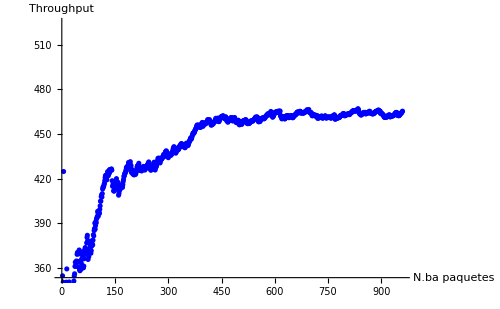
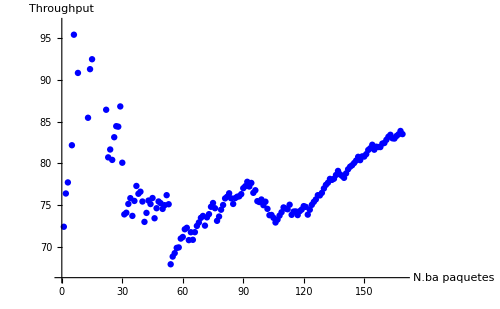
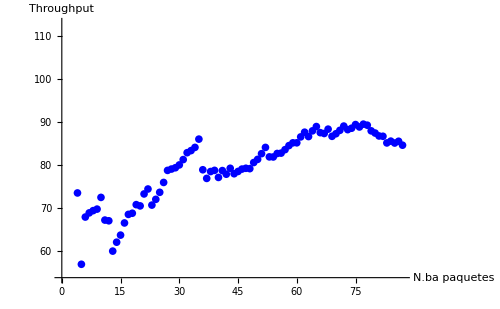
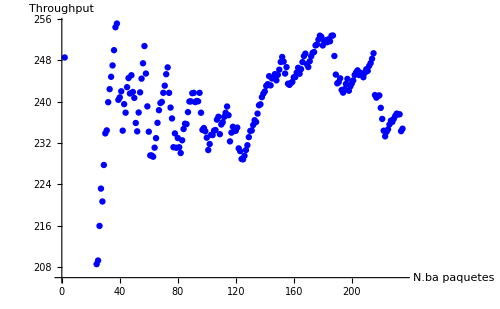
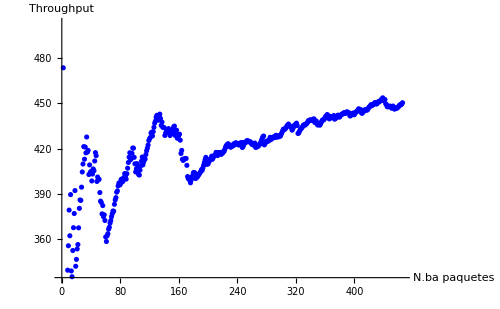
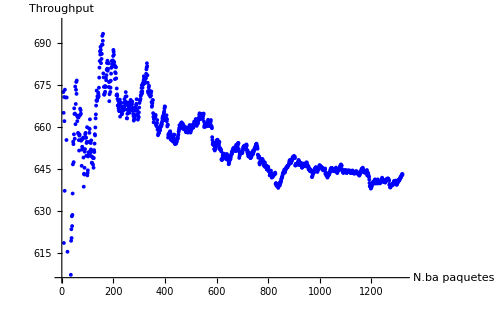
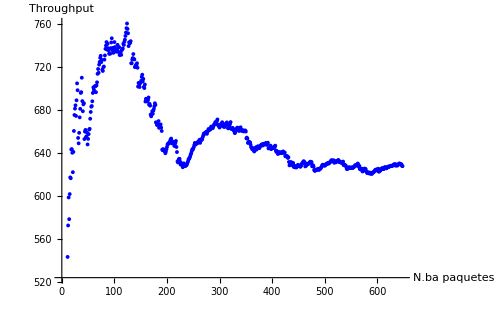
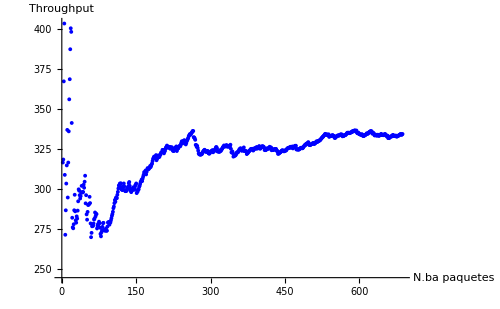
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10
```

```mathematica
ThroughputMax[paquetes123]
ThroughputMax[paquetes124]
ThroughputMax[paquetes1523]
ThroughputMax[paquetes1524]
ThroughputMax[paquetes154]
ThroughputMax[paquetes23]
ThroughputMax[paquetes24]
ThroughputMax[paquetes523]
ThroughputMax[paquetes524]
ThroughputMax[paquetes54] 
Last[paquetes123]
Last[paquetes123][[9]]
Length[paquetes123]
(Length[paquetes123]/Last[paquetes123][[1]])//N
```

465.368

450.44

83.5047

84.5347

234.749

642.982

627.655

334.29

312.263

999.517

{2.06288,231.745,3137,0,0,1917,1,{Ori-1,2,3},1.00001}

1.00001

960

465.368

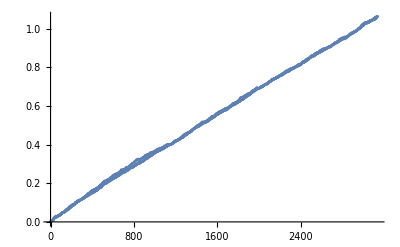

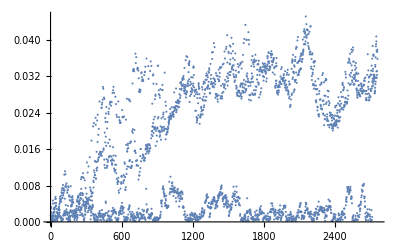

```mathematica
(*Obtencion del retardo extremo a extremo de cada paquete*)

out3;
out4;
ListPlot[Map[(#[[1]]-#[[9]])&,out3]]
ListPlot[Map[(#[[1]]-#[[9]])&,out4]]
```

# 7B.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo S&W

```mathematica
(*Ejecución de la función*)
opcionesDistintas3SW=ObtenerOpcionesDistintas[out3SW]
opcionesDistintas4SW=ObtenerOpcionesDistintas[out4SW]

paquetes123SW = getPacketsWithRoute[out3SW,{"Ori-1",2,3}];
paquetes1523SW = getPacketsWithRoute[out3SW,{"Ori-1",5,2,3}];
paquetes1524SW = getPacketsWithRoute[out4SW,{"Ori-1",5,2,4}];
paquetes154SW = getPacketsWithRoute[out4SW,{"Ori-1",5,4}];
paquetes124SW = getPacketsWithRoute[out4SW,{"Ori-1",2,4}]; 
paquetes23SW= getPacketsWithRoute[out3SW,{"Ori-2",2,3}];
paquetes24SW = getPacketsWithRoute[out4SW,{"Ori-2",2,4}]; 
paquetes523SW = getPacketsWithRoute[out3SW,{"Ori-5",5,2,3}];
paquetes524SW = getPacketsWithRoute[out4SW,{"Ori-5",5,2,4}]; 
paquetes54SW = getPacketsWithRoute[out4SW,{"Ori-5",5,4}]; 

tot1SW = Length[out3SW]+Length[out4SW]
tot2SW = Length[paquetes123SW]+ Length[paquetes1523SW]+Length[paquetes154SW]+Length[paquetes1524SW]+ Length[paquetes124SW]+Length[paquetes23SW]+Length[paquetes24SW]+Length[paquetes523SW]+Length[paquetes524SW]+Length[paquetes54SW]
```

{{Ori-2,2,3},{Ori-1,2,3},{Ori-5,5,2,3},{Ori-1,5,2,3}}

{{Ori-2,2,4},{Ori-1,5,4},{Ori-5,5,2,4},{Ori-5,5,4},{Ori-1,2,4},{Ori-1,5,2,4}}

6076

6076

```mathematica
t123 = getRetardo[paquetes123SW]
t124= getRetardo[paquetes124SW]
t1523 = getRetardo[paquetes1523SW]
t1524 = getRetardo[paquetes1524SW]
t154 = getRetardo[paquetes154SW]
t23 = getRetardo[paquetes23SW]
t24 = getRetardo[paquetes24SW]
t523 = getRetardo[paquetes523SW]
t524 = getRetardo[paquetes524SW]
t54 = getRetardo[paquetes54SW]
```

0.221887

0.998188

0.157096

0.870797

0.0523376

0.0930953

0.741883

0.130501

0.830823

0.0489747

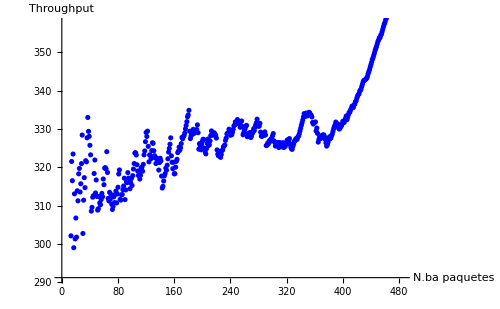
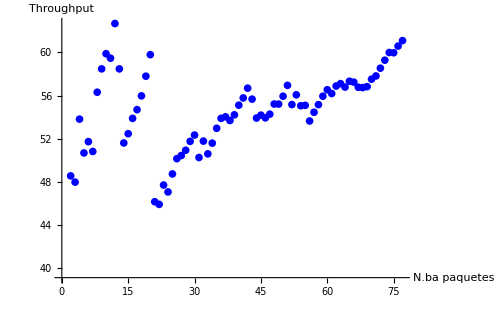
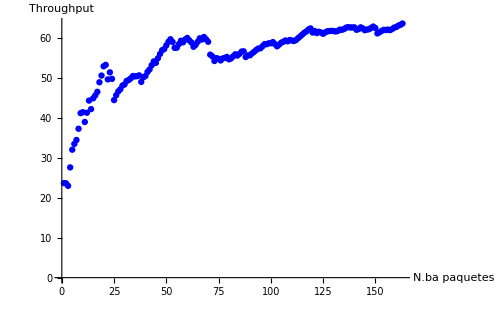
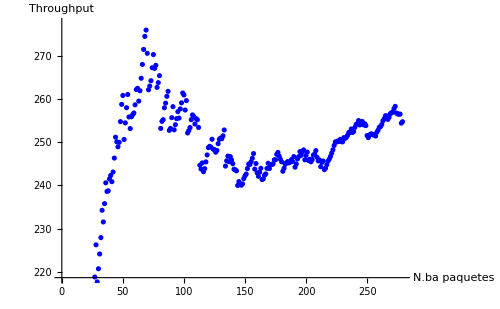
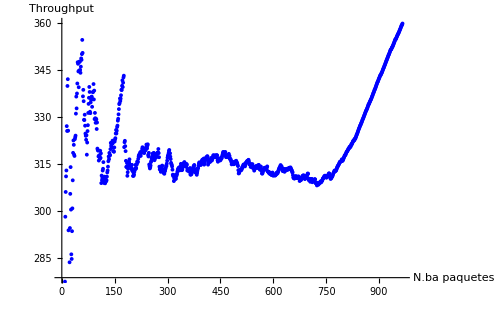
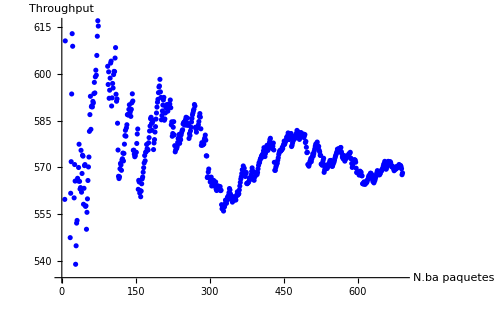
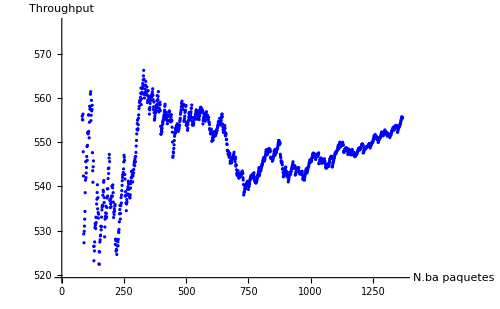
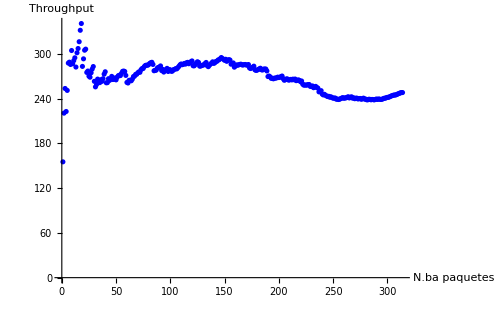
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10SW=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10SW
```

```mathematica
ThroughputMax[paquetes123SW]
ThroughputMax[paquetes124SW]
ThroughputMax[paquetes1523SW]
ThroughputMax[paquetes1524SW]
ThroughputMax[paquetes154SW]
ThroughputMax[paquetes23SW]
ThroughputMax[paquetes24SW]
ThroughputMax[paquetes523SW]
ThroughputMax[paquetes524SW]
ThroughputMax[paquetes54SW]
```

372.051

359.904

61.0825

63.5029

254.767

568.166

555.516

248.202

284.466

912.335

{{0.000781924,1422.05,1,0,0,1,1,{Ori-2,2,3},0.000170866},{0.00151773,704.315,2,0,0,5,1,{Ori-2,2,3},0.00113097},{0.00263726,181.12,3,0,1,2,1,{Ori-1,2,3},0.000159101},{0.00388699,2932.45,4,0,0,8,1,{Ori-2,2,3},0.00217093},{0.00594642,2228.43,5,0,1,9,1,{Ori-2,2,3},0.00219536},{0.00643946,511.062,6,0,0,3,1,{Ori-5,5,2,3},0.00155824},{0.00722119,1434.84,7,0,0,13,1,{Ori-2,2,3},0.00266408},{0.00863951,3471.96,8,0,0,3,1,{Ori-1,2,3},0.000537064},{0.00906638,299.333,9,0,0,6,1,{Ori-5,5,2,3},0.00342702},{0.0107208,4227.57,10,0,0,15,1,{Ori-2,2,3},0.00421301}}

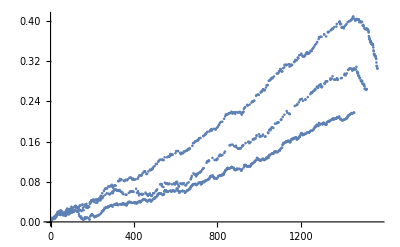

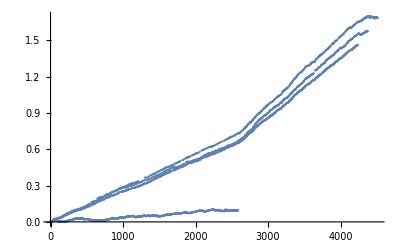

```mathematica
out3SW[[1;;10]]
out4SW;
ListPlot[Map[(#[[1]]-#[[9]])&,out3SW]]
ListPlot[Map[(#[[1]]-#[[9]])&,out4SW]]
```

# 7C.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo GBN

```mathematica
(*Ejecución de la función*)
opcionesDistintas3GBN=ObtenerOpcionesDistintas[out3GBN]
opcionesDistintas4GBN=ObtenerOpcionesDistintas[out4GBN]

paquetes123GBN = getPacketsWithRoute[out3GBN,{"Ori-1",2,3}];
paquetes1523GBN = getPacketsWithRoute[out3GBN,{"Ori-1",5,2,3}];
paquetes1524GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,2,4}];
paquetes154GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,4}];
paquetes124GBN = getPacketsWithRoute[out4GBN,{"Ori-1",2,4}]; 
paquetes23GBN= getPacketsWithRoute[out3GBN,{"Ori-2",2,3}];
paquetes24GBN = getPacketsWithRoute[out4GBN,{"Ori-2",2,4}]; 
paquetes523GBN = getPacketsWithRoute[out3GBN,{"Ori-5",5,2,3}];
paquetes524GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,2,4}]; 
paquetes54GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,4}]; 

tot1GBN = Length[out3GBN]+Length[out4GBN]
tot2GBN = Length[paquetes123GBN]+ Length[paquetes1523GBN]+Length[paquetes154GBN]+Length[paquetes1524GBN]+ Length[paquetes124GBN]+Length[paquetes23GBN]+Length[paquetes24GBN]+Length[paquetes523GBN]+Length[paquetes524GBN]+Length[paquetes54GBN]
```

{{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,2,3},{Ori-1,5,2,3}}

{{Ori-5,5,4},{Ori-1,5,2,4},{Ori-1,2,4},{Ori-1,5,4},{Ori-2,2,4},{Ori-5,5,2,4}}

5931

5931

```mathematica
t123 = getRetardo[paquetes123GBN]
t124= getRetardo[paquetes124GBN]
t1523 = getRetardo[paquetes1523GBN]
t1524 = getRetardo[paquetes1524GBN]
t154 = getRetardo[paquetes154GBN]
t23 = getRetardo[paquetes23GBN]
t24 = getRetardo[paquetes24GBN]
t523 = getRetardo[paquetes523GBN]
t524 = getRetardo[paquetes524GBN]
t54 = getRetardo[paquetes54GBN]
```

0.258524

0.00668587

0.26573

0.00726924

0.00246819

0.259418

0.00444381

0.270924

0.00639715

0.001754

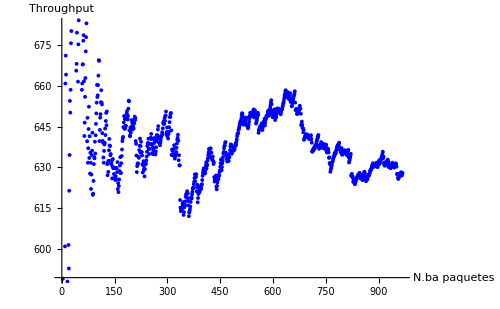
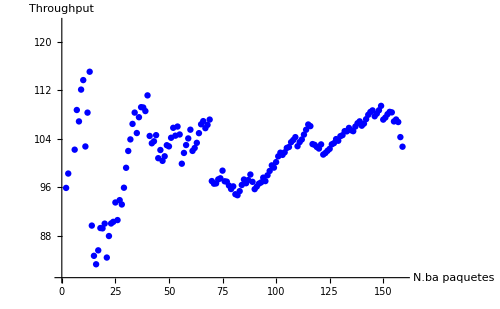
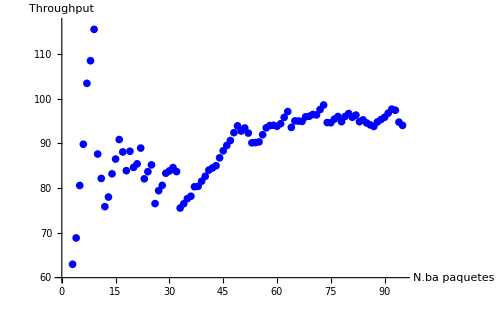
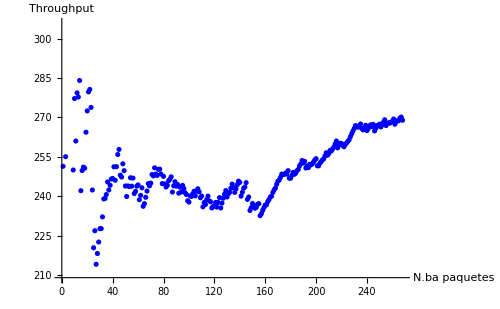
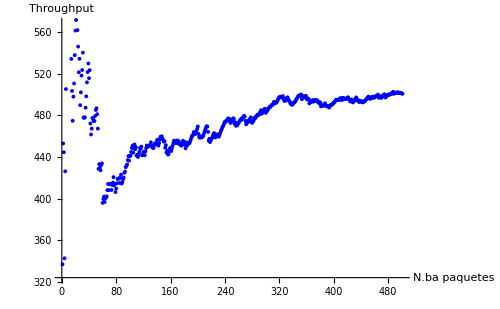
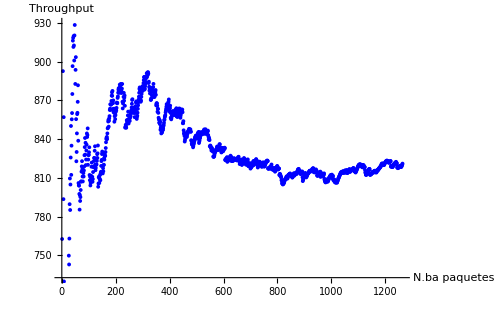
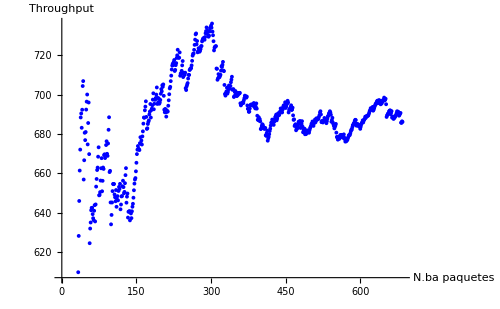
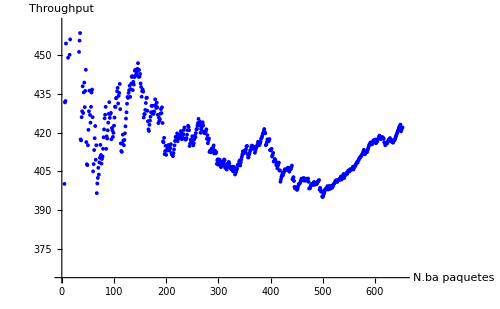
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10GBN=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10GBN
```

```mathematica
ThroughputMax[paquetes123GBN]
ThroughputMax[paquetes124GBN]
ThroughputMax[paquetes1523GBN]
ThroughputMax[paquetes1524GBN]
ThroughputMax[paquetes154GBN]
ThroughputMax[paquetes23GBN]
ThroughputMax[paquetes24GBN]
ThroughputMax[paquetes523GBN]
ThroughputMax[paquetes524GBN]
ThroughputMax[paquetes54GBN]
```

627.999

500.58

102.708

94.0612

268.949

821.093

686.189

421.954

336.638

997.422

{{0.00131112,2476.75,1,0,0,1,1,{Ori-2,2,3},0.00037047},{0.00139207,259.043,2,0,0,1,1,{Ori-5,5,2,3},0.000136246},{0.00163903,790.271,3,0,0,2,1,{Ori-2,2,3},0.000864386},{0.00173405,304.052,4,0,0,3,1,{Ori-2,2,3},0.001011},{0.00231577,1861.52,5,0,0,1,1,{Ori-1,2,3},0.000397604},{0.00314629,795.494,6,0,1,2,1,{Ori-5,5,2,3},0.000334261},{0.00343972,938.975,7,0,0,4,1,{Ori-1,5,2,3},0.000828987},{0.0042956,2738.83,8,0,0,2,1,{Ori-1,2,3},0.000525737},{0.00448066,592.185,9,0,0,4,1,{Ori-2,2,3},0.00204923},{0.00509117,443.482,10,0,1,5,1,{Ori-1,2,3},0.00110182},{0.0059686,870.551,11,0,1,4,1,{Ori-5,5,2,3},0.00245068},{0.00751874,4960.45,12,0,0,5,1,{Ori-2,2,3},0.00319241},{0.00756081,134.644,13,0,0,6,1,{Ori-2,2,3},0.00376347},{0.00757059,31.2735,14,0,0,9,1,{Ori-1,2,3},0.00231562},{0.0081674,1909.79,15,0,0,7,1,{Ori-2,2,3},0.00415505},{0.0109617,2269.43,16,0,2,8,1,{Ori-2,2,3},0.0042961},{0.0121826,1420.21,17,0,1,10,1,{Ori-1,2,3},0.00242395},{0.0124325,799.548,18,0,0,7,1,{Ori-5,5,2,3},0.00423719},{0.0124935,195.348,19,0,0,8,1,{Ori-5,5,2,3},0.00456248},{0.0127099,692.39,20,0,0,12,1,{Ori-1,2,3},0.00319023},{0.01355,2688.44,21,0,0,10,1,{Ori-2,2,3},0.0064688},{0.013901,28.1703,22,0,1,11,1,{Ori-5,5,2,3},0.00641456},{0.0142311,1056.49,23,0,0,11,1,{Ori-2,2,3},0.00685476},{0.0147966,371.347,24,0,1,15,1,{Ori-1,2,3},0.00447286},{0.0149553,508.045,25,0,0,16,1,{Ori-1,2,3},0.00492385},{0.0149731,56.8523,26,0,0,17,1,{Ori-1,2,3},0.00535209},{0.0151344,516.105,27,0,0,18,1,{Ori-1,2,3},0.00548662},{0.016199,3406.84,28,0,0,13,1,{Ori-5,5,2,3},0.00666835},{0.0163946,625.807,29,0,0,19,1,{Ori-1,2,3},0.00639184},{0.0176095,1410.59,30,0,1,16,1,{Ori-5,5,2,3},0.0076873},{0.0179019,935.667,31,0,0,12,1,{Ori-2,2,3},0.008514},{0.0180718,543.588,32,0,0,21,1,{Ori-1,2,3},0.00731736},{0.0185578,1555.24,33,0,0,17,1,{Ori-5,5,2,3},0.00770753},{0.0186803,392.147,34,0,0,22,1,{Ori-1,2,3},0.00814965},{0.019169,1563.55,35,0,0,18,1,{Ori-5,5,2,3},0.00888071},{0.0192304,196.69,36,0,0,13,1,{Ori-2,2,3},0.0097044},{0.0195659,1073.65,37,0,0,19,1,{Ori-5,5,2,3},0.00936072},{0.0197417,562.421,38,0,0,27,1,{Ori-1,2,3},0.0100926},{0.0208485,3541.73,39,0,0,20,1,{Ori-1,5,2,3},0.00709718},{0.0215886,650.886,40,0,1,32,1,{Ori-1,2,3},0.0109105},{0.024145,3556.92,41,0,1,15,1,{Ori-2,2,3},0.0123782},{0.0250575,926.669,42,0,1,16,1,{Ori-2,2,3},0.0126561},{0.0265096,1789.93,43,0,1,17,1,{Ori-2,2,3},0.0132016},{0.0267365,726.055,44,0,0,21,1,{Ori-5,5,2,3},0.0119113},{0.0272009,1486.33,45,0,0,37,1,{Ori-1,2,3},0.0128022},{0.0272509,159.828,46,0,0,22,1,{Ori-5,5,2,3},0.0124226},{0.0272914,129.768,47,0,0,23,1,{Ori-5,5,2,3},0.0126342},{0.0273085,54.7261,48,0,0,18,1,{Ori-2,2,3},0.0143398},{0.0285723,1488.73,49,0,1,19,1,{Ori-2,2,3},0.0150978},{0.0286228,161.514,50,0,0,20,1,{Ori-2,2,3},0.015737},{0.028697,237.496,51,0,0,21,1,{Ori-2,2,3},0.0157514},{0.0289768,895.463,52,0,0,40,1,{Ori-1,2,3},0.0161862},{0.029914,2998.94,53,0,0,22,1,{Ori-2,2,3},0.0167716},{0.0305208,1941.86,54,0,0,41,1,{Ori-1,5,2,3},0.017653},{0.0307021,579.862,55,0,0,28,1,{Ori-2,2,3},0.0211442},{0.0310184,1012.19,56,0,0,44,1,{Ori-1,2,3},0.0209725},{0.0310434,80.0769,57,0,0,48,1,{Ori-1,5,2,3},0.0225869},{0.0315819,1723.12,58,0,0,45,1,{Ori-1,2,3},0.0210957},{0.0328997,694.548,59,0,2,29,1,{Ori-2,2,3},0.0233371},{0.0333356,1394.93,60,0,0,41,1,{Ori-5,5,2,3},0.022938},{0.0337275,1254.24,61,0,0,46,1,{Ori-1,2,3},0.0212196},{0.033791,202.941,62,0,0,47,1,{Ori-1,2,3},0.022561},{0.033841,160.028,63,0,0,30,1,{Ori-2,2,3},0.0244594},{0.0343765,1713.6,64,0,0,31,1,{Ori-2,2,3},0.0246789},{0.0344746,314.168,65,0,0,32,1,{Ori-2,2,3},0.0249167},{0.0346697,624.233,66,0,0,50,1,{Ori-1,2,3},0.0251772},{0.0346752,17.5698,67,0,0,33,1,{Ori-2,2,3},0.0255814},{0.0350965,1348.16,68,0,0,44,1,{Ori-5,5,2,3},0.0253068},{0.0351485,166.514,69,0,0,51,1,{Ori-1,2,3},0.0260578},{0.0359859,2679.63,70,0,0,45,1,{Ori-5,5,2,3},0.0255831},{0.0360636,248.426,71,0,0,56,1,{Ori-1,5,2,3},0.0269982},{0.0363398,883.84,72,0,0,36,1,{Ori-2,2,3},0.0279395},{0.0366953,1137.79,73,0,0,37,1,{Ori-2,2,3},0.0284466},{0.0367239,91.4788,74,0,0,38,1,{Ori-2,2,3},0.0286962},{0.0369177,620.27,75,0,0,53,1,{Ori-1,2,3},0.0265888},{0.0370557,441.379,76,0,0,40,1,{Ori-2,2,3},0.0298166},{0.0379679,2919.09,77,0,0,54,1,{Ori-1,2,3},0.0267526},{0.03849,302.082,78,0,1,55,1,{Ori-1,2,3},0.0268752},{0.0386364,468.43,79,0,0,49,1,{Ori-5,5,2,3},0.0313223},{0.039482,2705.86,80,0,0,43,1,{Ori-2,2,3},0.032369},{0.0397074,721.417,81,0,0,59,1,{Ori-1,2,3},0.0273095},{0.0397562,156.195,82,0,0,44,1,{Ori-2,2,3},0.0324239},{0.0398099,171.594,83,0,0,50,1,{Ori-5,5,2,3},0.0323483},{0.0399598,479.911,84,0,0,47,1,{Ori-2,2,3},0.0331128},{0.0399886,92.1696,85,0,0,49,1,{Ori-2,2,3},0.033682},{0.0406192,2017.79,86,0,0,63,1,{Ori-1,2,3},0.0297169},{0.0406955,244.161,87,0,0,64,1,{Ori-1,2,3},0.0303085},{0.0412362,331.754,88,0,1,65,1,{Ori-1,2,3},0.0305851},{0.0425678,1597.19,89,0,1,51,1,{Ori-5,5,2,3},0.0335994},{0.043083,1648.91,90,0,0,52,1,{Ori-2,2,3},0.0353618},{0.0431139,98.6566,91,0,0,53,1,{Ori-2,2,3},0.0356132},{0.0432539,448.064,92,0,0,54,1,{Ori-2,2,3},0.0361658},{0.0436633,1310.11,93,0,0,68,1,{Ori-1,2,3},0.0333669},{0.0437548,292.68,94,0,0,69,1,{Ori-1,2,3},0.0347337},{0.0441732,1338.88,95,0,0,55,1,{Ori-2,2,3},0.0363749},{0.044224,162.803,96,0,0,56,1,{Ori-5,5,2,3},0.0361847},{0.0445706,21.105,97,0,1,56,1,{Ori-2,2,3},0.0364405},{0.0446136,137.655,98,0,0,57,1,{Ori-2,2,3},0.0364411},{0.0447315,377.445,99,0,0,57,1,{Ori-5,5,2,3},0.0364999},{0.0447435,38.2144,100,0,0,59,1,{Ori-2,2,3},0.0368591}}

{{0.90785,1165.58,1800,0,0,1160,1,{Ori-2,2,3},0.597935},{0.907941,292.384,1801,0,0,1177,1,{Ori-1,2,3},0.597615},{0.907998,181.984,1802,0,0,1162,1,{Ori-2,2,3},0.599781},{0.908086,281.748,1803,0,0,1181,1,{Ori-1,2,3},0.599576},{0.908388,968.531,1804,0,0,1182,1,{Ori-1,2,3},0.600437},{0.908562,553.981,1805,0,0,1183,1,{Ori-1,2,3},0.600997},{0.908631,221.418,1806,0,0,1166,1,{Ori-2,2,3},0.60144},{0.908911,895.35,1807,0,0,1184,1,{Ori-1,2,3},0.601117},{0.91041,1865.4,1808,0,1,1177,1,{Ori-5,5,2,3},0.597473},{0.911071,2114.29,1809,0,0,1169,1,{Ori-2,2,3},0.602936},{0.912443,4392.3,1810,0,0,1185,1,{Ori-1,2,3},0.601377},{0.912698,815.858,1811,0,0,1179,1,{Ori-5,5,2,3},0.598851},{0.913571,863.04,1812,0,1,1170,1,{Ori-2,2,3},0.603461},{0.913602,98.6415,1813,0,0,1182,1,{Ori-5,5,2,3},0.598999},{0.914695,3498.42,1814,0,0,1183,1,{Ori-5,5,2,3},0.599105},{0.914705,31.1341,1815,0,0,1185,1,{Ori-5,5,2,3},0.599209},{0.915031,1045.65,1816,0,0,1173,1,{Ori-2,2,3},0.605051},{0.916398,1653.78,1817,0,1,1189,1,{Ori-5,5,2,3},0.600891},{0.917241,2696.6,1818,0,0,1187,1,{Ori-1,2,3},0.603446},{0.917303,199.66,1819,0,0,1176,1,{Ori-2,2,3},0.606589},{0.917384,259.142,1820,0,0,1177,1,{Ori-2,2,3},0.606793},{0.9174,48.6214,1821,0,0,1197,1,{Ori-5,5,2,3},0.604334},{0.917852,190.258,1822,0,1,1198,1,{Ori-5,5,2,3},0.605059},{0.918187,1071.14,1823,0,0,1191,1,{Ori-1,5,2,3},0.605299},{0.919271,1202.22,1824,0,1,1178,1,{Ori-2,2,3},0.607468},{0.919291,63.1179,1825,0,0,1179,1,{Ori-2,2,3},0.607738},{0.919652,1154.03,1826,0,0,1203,1,{Ori-5,5,2,3},0.606953},{0.919774,391.707,1827,0,0,1180,1,{Ori-2,2,3},0.60799},{0.920128,1131.5,1828,0,0,1204,1,{Ori-5,5,2,3},0.607144},{0.920488,1152.58,1829,0,0,1190,1,{Ori-1,2,3},0.604969},{0.920587,318.768,1830,0,0,1183,1,{Ori-2,2,3},0.608826},{0.920836,794.243,1831,0,0,1205,1,{Ori-5,5,2,3},0.607345},{0.921161,1041.16,1832,0,0,1184,1,{Ori-2,2,3},0.609536},{0.921331,545.064,1833,0,0,1185,1,{Ori-2,2,3},0.609689},{0.922237,2899.1,1834,0,0,1187,1,{Ori-2,2,3},0.609817},{0.923808,1980.09,1835,0,1,1192,1,{Ori-1,2,3},0.606312},{0.923937,412.649,1836,0,0,1188,1,{Ori-2,2,3},0.610142},{0.924877,3007.15,1837,0,0,1190,1,{Ori-2,2,3},0.610509},{0.924958,260.343,1838,0,0,1197,1,{Ori-1,2,3},0.608536},{0.925167,666.955,1839,0,0,1198,1,{Ori-1,2,3},0.609683},{0.925262,305.676,1840,0,0,1192,1,{Ori-2,2,3},0.611538},{0.925761,1596.32,1841,0,0,1211,1,{Ori-5,5,2,3},0.611302},{0.926466,2256.,1842,0,0,1199,1,{Ori-1,2,3},0.610373},{0.926833,53.7863,1843,0,1,1193,1,{Ori-2,2,3},0.612464},{0.927486,2090.15,1844,0,0,1200,1,{Ori-1,2,3},0.610543},{0.927693,662.362,1845,0,0,1201,1,{Ori-1,2,3},0.610712},{0.92825,1783.45,1846,0,0,1194,1,{Ori-2,2,3},0.613072},{0.928883,2024.6,1847,0,0,1202,1,{Ori-1,2,3},0.611124},{0.92925,1174.39,1848,0,0,1213,1,{Ori-5,5,2,3},0.612487},{0.935762,4409.62,1849,0,3,1196,1,{Ori-2,2,3},0.613795},{0.936118,1139.88,1850,0,0,1205,1,{Ori-1,2,3},0.611856},{0.936164,145.58,1851,0,0,1206,1,{Ori-1,2,3},0.612016},{0.93732,3697.97,1852,0,0,1197,1,{Ori-2,2,3},0.614265},{0.938054,641.368,1853,0,1,1208,1,{Ori-1,2,3},0.612859},{0.938558,273.278,1854,0,1,1209,1,{Ori-1,2,3},0.613277},{0.938753,626.004,1855,0,0,1198,1,{Ori-2,2,3},0.615553},{0.938777,76.4449,1856,0,0,1211,1,{Ori-1,2,3},0.614143},{0.93951,2346.02,1857,0,0,1199,1,{Ori-2,2,3},0.615792},{0.940058,1751.54,1858,0,0,1212,1,{Ori-1,2,3},0.615144},{0.940164,338.599,1859,0,0,1215,1,{Ori-1,5,2,3},0.615747},{0.940403,765.17,1860,0,0,1201,1,{Ori-2,2,3},0.616427},{0.940442,126.39,1861,0,0,1213,1,{Ori-1,2,3},0.615281},{0.940691,794.917,1862,0,0,1216,1,{Ori-1,2,3},0.615937},{0.941653,1006.49,1863,0,1,1202,1,{Ori-2,2,3},0.616945},{0.941887,748.875,1864,0,0,1221,1,{Ori-5,5,2,3},0.616207},{0.942907,1097.84,1865,0,1,1203,1,{Ori-2,2,3},0.61721},{0.943015,347.555,1866,0,0,1218,1,{Ori-1,2,3},0.616709},{0.943385,1184.98,1867,0,0,1204,1,{Ori-2,2,3},0.618075},{0.943644,827.442,1868,0,0,1222,1,{Ori-5,5,2,3},0.618179},{0.94397,1042.64,1869,0,0,1225,1,{Ori-5,5,2,3},0.619095},{0.944013,139.518,1870,0,0,1226,1,{Ori-5,5,2,3},0.61953},{0.944198,589.549,1871,0,0,1207,1,{Ori-2,2,3},0.619886},{0.944763,1807.46,1872,0,0,1219,1,{Ori-1,2,3},0.619376},{0.945547,721.025,1873,0,1,1220,1,{Ori-1,2,3},0.619439},{0.9463,672.823,1874,0,1,1221,1,{Ori-1,5,2,3},0.619826},{0.947205,2894.54,1875,0,0,1210,1,{Ori-2,2,3},0.621236},{0.947473,858.242,1876,0,0,1211,1,{Ori-2,2,3},0.621877},{0.947826,1129.05,1877,0,0,1230,1,{Ori-5,5,2,3},0.621428},{0.947955,413.152,1878,0,0,1212,1,{Ori-2,2,3},0.622069},{0.94814,590.792,1879,0,0,1213,1,{Ori-2,2,3},0.622114},{0.948212,231.376,1880,0,0,1226,1,{Ori-1,2,3},0.620795},{0.948295,264.996,1881,0,0,1214,1,{Ori-2,2,3},0.622592},{0.950522,3029.91,1882,0,1,1227,1,{Ori-1,2,3},0.621669},{0.950527,15.6743,1883,0,0,1232,1,{Ori-5,5,2,3},0.622584},{0.951192,2128.86,1884,0,0,1229,1,{Ori-1,2,3},0.621935},{0.952012,778.008,1885,0,1,1228,1,{Ori-1,5,2,3},0.621754},{0.952273,835.35,1886,0,0,1230,1,{Ori-1,2,3},0.622224},{0.952468,626.106,1887,0,0,1233,1,{Ori-5,5,2,3},0.623628},{0.953288,163.124,1888,0,2,1234,1,{Ori-5,5,2,3},0.623727},{0.953437,476.315,1889,0,0,1217,1,{Ori-2,2,3},0.624525},{0.953863,1363.43,1890,0,0,1218,1,{Ori-2,2,3},0.624692},{0.954532,2140.66,1891,0,0,1231,1,{Ori-1,2,3},0.62236},{0.956492,2603.41,1892,0,1,1221,1,{Ori-2,2,3},0.625859},{0.957211,2298.83,1893,0,0,1222,1,{Ori-2,2,3},0.626064},{0.957711,1602.71,1894,0,0,1234,1,{Ori-1,2,3},0.622813},{0.958093,76.6706,1895,0,1,1236,1,{Ori-1,2,3},0.623007},{0.958137,141.688,1896,0,0,1237,1,{Ori-1,2,3},0.6233},{0.958142,14.5638,1897,0,0,1223,1,{Ori-2,2,3},0.627029},{0.959622,1835.79,1898,0,1,1238,1,{Ori-1,2,3},0.623972},{0.959777,495.583,1899,0,0,1224,1,{Ori-2,2,3},0.627186},{0.960378,428.042,1900,0,1,1246,1,{Ori-1,5,2,3},0.626386}}

{0.000940652,0.00125583,0.000774646,0.00072305,0.00191817,0.00281203,0.00261073,0.00376987,0.00243143,0.00398935,0.00351792,0.00432633,0.00379734,0.00525497,0.00401234,0.00666556,0.00975868,0.00819529,0.00793105,0.00951967,0.00708124,0.00748642,0.00737636,0.0103237,0.0100315,0.009621,0.00964774,0.00953065,0.0100027,0.00992222,0.00938791,0.0107544,0.0108503,0.0105307,0.0102882,0.00952602,0.0102052,0.00964904,0.0137513,0.0106781,0.0117669,0.0124015,0.0133079,0.0148252,0.0143988,0.0148283,0.0146572,0.0129687,0.0134745,0.0128858,0.0129456,0.0127907,0.0131424,0.0128678,0.00955786,0.0100459,0.00845647,0.0104861,0.00956256,0.0103975,0.0125079,0.0112299,0.00938154,0.00969757,0.00955793,0.00949254,0.00909385,0.00978975,0.00909079,0.0104029,0.0090654,0.0084003,0.0082487,0.00802768,0.010329,0.00723907,0.0112153,0.0116148,0.00731408,0.00711298,0.0123979,0.00733234,0.00746159,0.00684702,0.00630659,0.0109023,0.010387,0.010651,0.00896832,0.00772124,0.00750069,0.00708808,0.0102964,0.00902105,0.00779825,0.00803933,0.00813006,0.0081725,0.0082316,0.00788439,0.00987099,0.00832592,0.0093647,0.0109735,0.00797418,0.00858126,0.0102897,0.0103478,0.00970543,0.0108526,0.00974141,0.0106219,0.0102349,0.0100688,0.00999139,0.0102793,0.010038,0.00985426,0.00912822,0.00937563,0.0136236,0.0133749,0.0134256,0.0132771,0.0133883,0.0124284,0.0145777,0.0137279,0.0173949,0.0139491,0.0146512,0.0177079,0.0179683,0.0171017,0.0157256,0.0161448,0.0174982,0.0161834,0.0165225,0.0163929,0.0160537,0.0169639,0.0173917,0.016768,0.0207045,0.0199694,0.0194608,0.0190023,0.0196773,0.0193151,0.0183458,0.0185332,0.0202626,0.0197534,0.0216405,0.0221417,0.0211885,0.0204531,0.021614,0.0217039,0.0209941,0.0222617,0.0236234,0.0231485,0.0239998,0.0261681,0.0254296,0.0266834,0.0285412,0.0265873,0.0254912,0.0261041,0.0269279,0.0261525,0.0283316,0.0259744,0.0260627,0.0255895,0.0259404,0.025434,0.0258325,0.0261149,0.0253326,0.0266262,0.0249505,0.0255592,0.0249961,0.0253455,0.0271387,0.0278345,0.028439,0.0282776,0.0277184,0.0276974,0.0292862,0.0285214,0.0310139,0.0293759,0.029808,0.0290273,0.0289987,0.0294019,0.0288629,0.0287421,0.0288549,0.0293959,0.0289503,0.0290453,0.0290722,0.0291661,0.0281238,0.0276555,0.0264164,0.0272533,0.0266431,0.0305348,0.0289734,0.0295445,0.0292297,0.0295989,0.0294503,0.0322442,0.0291947,0.0363591,0.0332718,0.0298757,0.03345,0.0327548,0.0287873,0.0375109,0.033319,0.0378947,0.0379864,0.0378204,0.031162,0.0309512,0.0313108,0.0345734,0.0342438,0.0318354,0.0340136,0.0337322,0.0331006,0.031899,0.032335,0.0402495,0.0399108,0.0366589,0.0350923,0.044078,0.0434525,0.0368857,0.0376701,0.0388706,0.0453534,0.0390225,0.0394608,0.0390904,0.0399143,0.039505,0.0468308,0.0394977,0.0449364,0.044009,0.0397211,0.0389285,0.0391629,0.0433545,0.0425436,0.0448718,0.0413775,0.0421,0.0431338,0.0487618,0.0433615,0.0434621,0.0435709,0.0480527,0.0469042,0.0439601,0.0465296,0.0442599,0.0453372,0.0442637,0.0451856,0.0451482,0.046679,0.0456284,0.0452534,0.0469409,0.0482303,0.0466756,0.0465002,0.0472022,0.0460933,0.0469175,0.0459857,0.0458837,0.0463431,0.0463358,0.0461716,0.0472196,0.0483816,0.0473622,0.0481082,0.0483827,0.0497192,0.0501351,0.0489032,0.0495702,0.048584,0.0467455,0.0469859,0.0469667,0.0495037,0.0476443,0.047538,0.0479059,0.047868,0.0478376,0.0575613,0.057552,0.0547277,0.0572858,0.0553954,0.0557059,0.0552819,0.0568274,0.0562588,0.0557025,0.056159,0.0534777,0.0548417,0.0553957,0.0541513,0.0539553,0.0536331,0.0549316,0.0555899,0.0548104,0.0577659,0.0580842,0.0566548,0.0583403,0.0557753,0.0578726,0.055956,0.056031,0.0568805,0.056304,0.0576445,0.0568594,0.0568226,0.057128,0.0592565,0.0583593,0.0589093,0.0608728,0.0635014,0.0618434,0.061769,0.0617248,0.0632534,0.063819,0.063291,0.0621902,0.0622494,0.0633539,0.0637181,0.0625227,0.0623472,0.0638474,0.0630419,0.0641138,0.0644105,0.0623943,0.0635867,0.0624268,0.062878,0.0631066,0.0634822,0.0628241,0.0623242,0.0625896,0.0633477,0.0624881,0.0626158,0.0641468,0.0622421,0.0618199,0.0623425,0.0632021,0.0630534,0.0629032,0.0631902,0.0637387,0.0643285,0.0644441,0.0641637,0.0651621,0.0648116,0.0649979,0.0650251,0.0705715,0.0671082,0.0650727,0.0677367,0.067174,0.0649675,0.0650992,0.065125,0.0659505,0.0656456,0.065247,0.0652085,0.0676225,0.0658184,0.0674069,0.0682122,0.0673067,0.0667449,0.066993,0.0661121,0.0660952,0.0655629,0.0652875,0.0651832,0.0655567,0.0642069,0.0641665,0.0658561,0.0649285,0.063299,0.0633875,0.0643973,0.066678,0.0669371,0.0664497,0.0670383,0.0669937,0.0673767,0.0670802,0.0670579,0.069476,0.0696209,0.0692182,0.0695643,0.0694053,0.0704008,0.0695684,0.0739101,0.0725538,0.0738406,0.0735752,0.0718947,0.0717006,0.0736025,0.0720147,0.0739812,0.074199,0.0741473,0.0745887,0.074267,0.0745714,0.0752693,0.0760759,0.0747537,0.0730789,0.0703049,0.0744578,0.0708054,0.0707015,0.0741185,0.0714988,0.0705602,0.0697311,0.0693508,0.0704979,0.0700984,0.0697163,0.0699417,0.0703503,0.0725024,0.0703192,0.0694809,0.0698455,0.0691301,0.0720068,0.0715547,0.0723073,0.0702678,0.0704065,0.0706811,0.0712217,0.0713557,0.0708425,0.0708337,0.0722916,0.0745184,0.0740462,0.0732797,0.072779,0.0745043,0.0739173,0.0745676,0.0747773,0.0745748,0.0738336,0.0739369,0.0735241,0.0744564,0.0735907,0.0730942,0.0731289,0.073141,0.0761094,0.0777225,0.0782893,0.076993,0.0807888,0.081324,0.0817449,0.0816131,0.0778137,0.0817638,0.0770464,0.0767729,0.0810469,0.0770882,0.0760662,0.0760352,0.0785184,0.0809027,0.0847455,0.0785974,0.0792015,0.0813755,0.0850566,0.0843307,0.0826049,0.0825339,0.0822706,0.0831608,0.0798693,0.0843839,0.0841451,0.0815018,0.0844765,0.0844755,0.0849498,0.0879314,0.0867069,0.0830641,0.0837765,0.0842308,0.0874154,0.0875677,0.0874087,0.0870458,0.0850102,0.0881468,0.0854616,0.0854862,0.0841988,0.0879207,0.0870198,0.0886235,0.0863552,0.0840032,0.086492,0.0846928,0.0847558,0.0843919,0.0839585,0.0851187,0.0907986,0.091262,0.0886382,0.0884626,0.0872193,0.0867176,0.0865823,0.0866871,0.0851734,0.0871186,0.0850419,0.0848402,0.0855521,0.0842538,0.0842467,0.083628,0.0829587,0.0855933,0.0820536,0.0823673,0.0845098,0.0838479,0.0838308,0.0838991,0.085317,0.0841953,0.0851398,0.0847086,0.0850731,0.0856082,0.0863561,0.0857891,0.0853881,0.0852262,0.0847007,0.0880331,0.085009,0.0843204,0.0885862,0.0889417,0.0873979,0.0876442,0.084777,0.0843884,0.0866203,0.085703,0.0864882,0.0837041,0.0847823,0.0848665,0.0850039,0.0846024,0.0851864,0.0859232,0.0870676,0.0868354,0.0860928,0.0876027,0.0867238,0.0870425,0.0853927,0.0860033,0.0875447,0.0867856,0.0875433,0.0873341,0.0907278,0.0884431,0.087273,0.0869216,0.085779,0.0848907,0.0873716,0.0857036,0.0857737,0.085055,0.0849641,0.0848843,0.084295,0.0857943,0.084472,0.0859351,0.0858489,0.0865305,0.0890528,0.0878831,0.0879029,0.0909595,0.0907511,0.0889669,0.0890829,0.0917862,0.0894154,0.0896674,0.0895503,0.089281,0.0906564,0.089227,0.0895323,0.0898265,0.0891447,0.088933,0.0890668,0.0880949,0.0898789,0.0900513,0.0948891,0.0948852,0.0952664,0.0928941,0.0915602,0.0912905,0.0916841,0.0933738,0.093402,0.0921906,0.0917913,0.0918401,0.0919578,0.0919043,0.0927191,0.0917075,0.0961486,0.0912896,0.0930864,0.0939535,0.093164,0.0935004,0.0934699,0.0935597,0.093741,0.0938299,0.0940254,0.0946062,0.0947362,0.0942908,0.0936828,0.0962724,0.0958314,0.0963765,0.0963511,0.0967088,0.0976556,0.0962379,0.0964952,0.0962798,0.096782,0.0960339,0.0963007,0.0963501,0.0961358,0.0962721,0.0964749,0.0960684,0.0965803,0.0958511,0.0958023,0.0977127,0.0970569,0.0958244,0.0953917,0.096039,0.0959833,0.0972444,0.0963699,0.0960375,0.0981476,0.0952509,0.0964825,0.0953651,0.0983817,0.0986927,0.0990796,0.101346,0.100674,0.101344,0.100546,0.101539,0.102719,0.102365,0.10347,0.101999,0.10387,0.103453,0.103862,0.103658,0.103279,0.103323,0.103358,0.103244,0.106991,0.106739,0.106893,0.104941,0.106554,0.108373,0.105824,0.107375,0.106584,0.105679,0.106969,0.106322,0.107173,0.106981,0.107237,0.106384,0.105985,0.108674,0.105843,0.106435,0.105635,0.106167,0.106427,0.106388,0.106196,0.109436,0.112679,0.111245,0.109862,0.111254,0.110109,0.110692,0.115024,0.110535,0.110594,0.110926,0.113967,0.110428,0.109958,0.110996,0.111135,0.110299,0.110193,0.110512,0.115949,0.113817,0.113215,0.11028,0.113444,0.11042,0.114108,0.112704,0.112725,0.113631,0.114177,0.116242,0.113889,0.116253,0.114551,0.119069,0.115604,0.118029,0.118739,0.119239,0.11581,0.119722,0.120183,0.120528,0.120477,0.11926,0.11667,0.116682,0.122549,0.117062,0.1161,0.116529,0.116097,0.122832,0.118334,0.116004,0.119626,0.127444,0.118454,0.127515,0.127878,0.122939,0.122935,0.121985,0.118618,0.122299,0.119809,0.122046,0.120029,0.120015,0.122733,0.122301,0.120394,0.122202,0.121207,0.122447,0.12189,0.126276,0.125273,0.128014,0.12397,0.123838,0.124458,0.124759,0.124246,0.130147,0.129215,0.1264,0.126775,0.12601,0.126713,0.126539,0.12744,0.128117,0.127922,0.127576,0.131927,0.129117,0.128309,0.132266,0.13132,0.130409,0.128244,0.128732,0.127224,0.129339,0.127032,0.126855,0.127124,0.127183,0.128155,0.128014,0.126654,0.126666,0.126447,0.128649,0.126818,0.128082,0.127016,0.126883,0.126894,0.126946,0.126248,0.126674,0.126858,0.126116,0.126279,0.13031,0.128306,0.127226,0.128035,0.127887,0.12849,0.128829,0.12886,0.128309,0.128835,0.129552,0.128429,0.129908,0.12881,0.128534,0.128717,0.134053,0.134926,0.134563,0.133446,0.134794,0.133955,0.133897,0.133946,0.138602,0.137683,0.137801,0.136551,0.135297,0.135655,0.135984,0.139153,0.136531,0.139425,0.139632,0.136879,0.138594,0.138627,0.138347,0.139964,0.137201,0.137629,0.137139,0.137541,0.136571,0.13587,0.135718,0.136127,0.136,0.135143,0.135309,0.137482,0.1359,0.137605,0.135823,0.136616,0.137831,0.140407,0.139469,0.138898,0.141053,0.141163,0.141669,0.139577,0.139459,0.139711,0.139688,0.142063,0.14273,0.142235,0.14163,0.140993,0.140532,0.143412,0.141412,0.144382,0.14432,0.140537,0.143321,0.146422,0.14522,0.143656,0.144336,0.147027,0.144787,0.145478,0.1449,0.148034,0.147295,0.147786,0.145234,0.144861,0.144534,0.144757,0.145699,0.146267,0.144743,0.145025,0.148885,0.146304,0.146832,0.146732,0.151383,0.148316,0.149837,0.149054,0.149766,0.149411,0.1494,0.148968,0.150269,0.150894,0.151088,0.151049,0.15125,0.150513,0.151753,0.149526,0.148672,0.149036,0.148484,0.148657,0.14712,0.148623,0.147851,0.149211,0.149268,0.149636,0.15133,0.151565,0.151709,0.150848,0.152108,0.151511,0.151462,0.156666,0.156146,0.154884,0.155463,0.155781,0.156131,0.15422,0.154152,0.154225,0.158478,0.159651,0.162076,0.161547,0.156301,0.162315,0.157898,0.157861,0.16445,0.165248,0.160427,0.166587,0.166591,0.17051,0.163206,0.163207,0.163511,0.165791,0.162811,0.16299,0.164901,0.171466,0.165764,0.166604,0.17411,0.171524,0.167704,0.167575,0.167557,0.174068,0.17203,0.16897,0.175752,0.168966,0.173553,0.169299,0.176904,0.169931,0.175409,0.177371,0.175228,0.177837,0.170146,0.170458,0.174592,0.179343,0.178533,0.171933,0.171722,0.176176,0.174048,0.173476,0.173847,0.174303,0.175532,0.184035,0.175814,0.175554,0.178284,0.177043,0.175693,0.17662,0.176873,0.176966,0.176905,0.177084,0.176995,0.178619,0.177559,0.178729,0.177519,0.179703,0.177257,0.177734,0.178744,0.177434,0.175735,0.175421,0.175457,0.178663,0.177503,0.1786,0.17831,0.178789,0.179967,0.18221,0.180166,0.180379,0.184006,0.183338,0.18303,0.182415,0.182552,0.182531,0.182754,0.183025,0.182828,0.183017,0.18489,0.184718,0.186432,0.184321,0.186496,0.185624,0.18449,0.186662,0.184342,0.184677,0.185833,0.183548,0.18608,0.186089,0.185005,0.183401,0.185543,0.185635,0.184921,0.186415,0.186181,0.184927,0.18477,0.185838,0.185104,0.184986,0.184932,0.184549,0.184544,0.184772,0.185,0.184052,0.183968,0.18443,0.184329,0.184524,0.185196,0.184726,0.185052,0.185115,0.188107,0.188634,0.188292,0.189205,0.188366,0.18723,0.190292,0.18723,0.188518,0.188358,0.188835,0.186171,0.185987,0.190173,0.186572,0.188527,0.18622,0.18622,0.186118,0.189244,0.18949,0.188266,0.187509,0.188292,0.187495,0.189852,0.189082,0.189789,0.189887,0.189952,0.189837,0.191454,0.190575,0.189112,0.188826,0.188619,0.188882,0.190011,0.190324,0.192019,0.191418,0.192816,0.1922,0.191917,0.193015,0.19341,0.196287,0.196081,0.195982,0.196261,0.193442,0.196692,0.194226,0.19465,0.194964,0.19476,0.198819,0.199154,0.199089,0.197395,0.200272,0.198297,0.197711,0.196612,0.197574,0.195776,0.200439,0.195313,0.195747,0.202569,0.197075,0.202386,0.197021,0.196409,0.196427,0.203298,0.202371,0.202325,0.196646,0.202744,0.203204,0.197629,0.197962,0.203555,0.19715,0.198251,0.206574,0.201392,0.199276,0.207477,0.200975,0.207803,0.200788,0.209883,0.209971,0.208818,0.207805,0.202031,0.201948,0.203158,0.202323,0.210911,0.20476,0.203519,0.211453,0.212146,0.212154,0.204696,0.21161,0.210524,0.210795,0.205529,0.210378,0.206277,0.205441,0.20648,0.210303,0.207035,0.208445,0.213218,0.212938,0.210659,0.209987,0.211733,0.210937,0.21168,0.211103,0.213542,0.212237,0.21222,0.212803,0.215148,0.214855,0.215906,0.216861,0.218438,0.21706,0.21887,0.218246,0.219763,0.217832,0.218787,0.218423,0.22035,0.221232,0.221485,0.222706,0.223928,0.223149,0.223951,0.223617,0.223522,0.223828,0.22386,0.224241,0.227267,0.224384,0.223843,0.225356,0.225227,0.226256,0.225796,0.225494,0.226491,0.227109,0.22562,0.225855,0.226655,0.226161,0.225558,0.224831,0.225977,0.226464,0.226756,0.226425,0.226559,0.227697,0.226487,0.226808,0.226851,0.226925,0.226769,0.226557,0.228138,0.226351,0.227823,0.233839,0.230152,0.2307,0.235221,0.229331,0.235155,0.234906,0.229683,0.235113,0.235347,0.230551,0.229668,0.229951,0.236628,0.236496,0.231605,0.238284,0.237765,0.231201,0.237207,0.237153,0.23652,0.234553,0.231362,0.230518,0.230385,0.230586,0.233008,0.237364,0.232346,0.233108,0.233149,0.235291,0.236695,0.234094,0.23372,0.24125,0.241406,0.24094,0.241222,0.239783,0.239706,0.233387,0.238707,0.23756,0.237053,0.23321,0.233065,0.237729,0.237057,0.232567,0.237941,0.239936,0.238708,0.236675,0.24352,0.241712,0.240031,0.245686,0.24082,0.240937,0.240625,0.2407,0.240597,0.240652,0.243974,0.24342,0.241252,0.241546,0.243318,0.24247,0.242031,0.243943,0.244479,0.24447,0.245692,0.24493,0.244991,0.245618,0.245572,0.246536,0.245494,0.245924,0.247917,0.247651,0.248997,0.247974,0.248469,0.246388,0.245729,0.245534,0.245467,0.244675,0.240947,0.244864,0.241212,0.241185,0.246402,0.241635,0.241655,0.243847,0.243786,0.246195,0.243933,0.246709,0.250662,0.245368,0.247892,0.247154,0.24707,0.246987,0.252526,0.252043,0.245772,0.246012,0.251106,0.248005,0.252457,0.253214,0.252415,0.248336,0.249419,0.253601,0.250259,0.251689,0.251487,0.254602,0.25225,0.251668,0.251594,0.254763,0.25502,0.252283,0.25232,0.256442,0.256346,0.253408,0.253751,0.255311,0.257142,0.257217,0.257674,0.256821,0.256897,0.254295,0.25433,0.257287,0.256768,0.256672,0.254678,0.255988,0.254623,0.253955,0.254609,0.2548,0.25505,0.255813,0.255579,0.25547,0.255922,0.257181,0.256402,0.257745,0.256656,0.256715,0.257159,0.257683,0.258809,0.259107,0.258387,0.258537,0.256591,0.257099,0.257738,0.256125,0.258582,0.2584,0.258593,0.258834,0.258769,0.260645,0.259793,0.260294,0.260377,0.261351,0.261722,0.264793,0.263732,0.264687,0.26519,0.265007,0.265505,0.26532,0.265948,0.265216,0.267758,0.267365,0.267772,0.266636,0.266739,0.266465,0.267162,0.267421,0.268766,0.268034,0.268426,0.268999,0.26902,0.26822,0.268979,0.270703,0.270401,0.268667,0.270772,0.270435,0.27004,0.272868,0.272903,0.27366,0.273904,0.274118,0.275083,0.274708,0.275027,0.27498,0.274901,0.275246,0.272766,0.272968,0.277617,0.278576,0.280223,0.278772,0.277726,0.277037,0.277463,0.275386,0.279039,0.274386,0.274352,0.27475,0.275543,0.280124,0.27822,0.276784,0.27774,0.277273,0.278314,0.278043,0.277409,0.278695,0.278838,0.279903,0.27875,0.27841,0.280446,0.279834,0.280565,0.279808,0.279354,0.279356,0.280553,0.280722,0.279797,0.280128,0.282473,0.282478,0.283082,0.281313,0.283471,0.280966,0.280792,0.286519,0.286435,0.285828,0.286002,0.285416,0.284343,0.28802,0.287282,0.286127,0.285656,0.286527,0.286228,0.286205,0.286655,0.28859,0.28781,0.288163,0.288488,0.287876,0.288148,0.287089,0.287223,0.289999,0.288502,0.291452,0.292717,0.292769,0.292246,0.291981,0.293881,0.294139,0.293866,0.293721,0.293487,0.292943,0.29239,0.293396,0.292627,0.292888,0.293749,0.293755,0.293913,0.294995,0.295307,0.295467,0.295621,0.296417,0.296614,0.297204,0.301651,0.297119,0.301827,0.301656,0.302302,0.305588,0.306183,0.30193,0.302149,0.301914,0.302403,0.303009,0.303339,0.303483,0.302771,0.302408,0.301983,0.303878,0.301605,0.301067,0.300637,0.300525,0.300132,0.300632,0.299874,0.301285,0.30155,0.301172,0.301216,0.301172,0.3006,0.300074,0.300668,0.30213,0.302186,0.3014,0.30254,0.304762,0.30464,0.305189,0.306236,0.306009,0.306753,0.306512,0.306504,0.306391,0.307622,0.3072,0.307936,0.307954,0.307508,0.308017,0.306974,0.306765,0.306578,0.306455,0.306604,0.306661,0.306846,0.307092,0.308229,0.311378,0.311171,0.310511,0.311116,0.311346,0.311591,0.31204,0.309708,0.309954,0.309299,0.309991,0.310043,0.309324,0.308416,0.30918,0.307881,0.308086,0.308277,0.308295,0.309338,0.308733,0.308665,0.307994,0.308021,0.309453,0.308493,0.309655,0.309794,0.309246,0.309172,0.309906,0.310518,0.310295,0.309914,0.310325,0.308217,0.308509,0.307952,0.307565,0.307191,0.307793,0.312937,0.308135,0.311066,0.313847,0.31011,0.314603,0.31559,0.315495,0.30998,0.315507,0.313795,0.310714,0.310592,0.313065,0.312793,0.312888,0.311803,0.311553,0.312699,0.311784,0.312983,0.315518,0.311761,0.313491,0.311625,0.311642,0.312421,0.317496,0.313795,0.314368,0.316422,0.315483,0.313724,0.314459,0.316093,0.314369,0.316943,0.316981,0.315178,0.317759,0.316764,0.321967,0.324263,0.324148,0.323055,0.325194,0.325281,0.3232,0.324635,0.323718,0.324913,0.324416,0.323976,0.325162,0.324754,0.324708,0.32568,0.325697,0.326307,0.325311,0.325465,0.324875,0.324484,0.324312,0.325387,0.326107,0.326474,0.325969,0.325596,0.326398,0.325886,0.326025,0.327417,0.325702,0.328853,0.327943,0.329257,0.330257,0.330049,0.32884,0.32956,0.328911,0.329171,0.332172,0.330633,0.331147,0.334899,0.335086,0.334837,0.331112,0.33565,0.332591,0.333992,0.337084,0.336015,0.333349,0.336744,0.336872,0.333643,0.333628,0.335401,0.332885,0.336801,0.335962,0.33605,0.335738,0.3327,0.33512,0.334933,0.332392,0.335697,0.333528,0.334837,0.334333,0.337413,0.334373,0.335477,0.334027,0.33521,0.333754,0.333634,0.335074,0.335364,0.334471,0.335714,0.335025,0.335351,0.336007,0.335848,0.335843,0.335426,0.342996,0.337947,0.341141,0.337871,0.341773,0.338799,0.337984,0.341633,0.341516,0.337818,0.339744,0.340847,0.338832,0.340483,0.338866,0.341814,0.340033,0.342115,0.342091,0.342072,0.34843,0.345838,0.346502,0.346448,0.346186,0.346781,0.349285,0.348801,0.34851,0.347512,0.352657,0.35189,0.34788,0.349644,0.349933,0.351607,0.349587,0.35234,0.350901,0.349754,0.350655,0.349668,0.349078,0.350046,0.350134,0.350344,0.349938,0.351305,0.351862,0.351727,0.353007,0.353641,0.353682,0.353599,0.357694,0.358249,0.357551,0.358041,0.361259,0.360451,0.360026,0.360137,0.360222,0.35975,0.358714,0.360893,0.360435,0.3602,0.361174,0.361343,0.361744,0.360187,0.360368,0.360764,0.360074,0.36055,0.362285,0.363238,0.36079,0.360728,0.362254,0.361473,0.361595,0.361708,0.360121,0.36127,0.360337,0.36122,0.361242,0.36308,0.362671,0.363202,0.361441,0.361718,0.360963,0.361082,0.360189,0.360695,0.360284,0.360357,0.360063,0.360227,0.360085,0.360243,0.360135,0.360245,0.360515,0.361481,0.360121,0.36538,0.361699,0.359826,0.360246,0.362422,0.367863,0.367582,0.367461,0.363059,0.367983,0.361943,0.367421,0.365241,0.362563,0.362362,0.365062,0.367619,0.366089,0.365493,0.365718,0.365856,0.366197,0.367902,0.368451,0.36862,0.36838,0.366962,0.367687,0.368178,0.368127,0.370175,0.36835,0.368206,0.369643,0.367837,0.370544,0.370347,0.371592,0.372303,0.3719,0.37084,0.371323,0.37171,0.372195,0.372699,0.372404,0.373186,0.374885,0.374876,0.374169,0.375248,0.374674,0.374526,0.376978,0.376369,0.376514,0.376044,0.376036,0.376007,0.375556,0.375461,0.376273,0.379679,0.377285,0.377217,0.379852,0.377019,0.379918,0.378597,0.377974,0.37991,0.379755,0.379413,0.378933,0.380849,0.37768,0.379497,0.381174,0.378615,0.377122,0.38083,0.379001,0.376459,0.376413,0.376599,0.376737,0.377461,0.379403,0.377735,0.378238,0.380625,0.380351,0.382007,0.383025,0.381243,0.381959,0.382745,0.382816,0.386497,0.384333,0.383096,0.383092,0.383057,0.385651,0.386454,0.386161,0.389745,0.388638,0.387941,0.390137,0.389034,0.389301,0.38905,0.388329,0.39131,0.390439,0.390018,0.389483,0.389107,0.389316,0.388951,0.389627,0.38968,0.388478,0.388691,0.388528,0.391762,0.391787,0.393179,0.393536,0.39709,0.398516,0.396548,0.396833,0.400097,0.399605,0.397005,0.397258,0.396864,0.396474,0.398931,0.396973,0.400241,0.400876,0.398191,0.399418,0.398417,0.399795,0.400044,0.398259,0.399537,0.398583,0.399416,0.399669,0.401459,0.400164,0.401228,0.400948,0.401526,0.400884,0.402901,0.402539,0.40298,0.402594,0.403048,0.402542,0.402224,0.402439,0.402116,0.404873,0.402457,0.405584,0.404867,0.403957,0.401195,0.402065,0.401049,0.402896,0.402416,0.40196,0.403755,0.402448,0.402532,0.402901,0.403948,0.403024,0.403536,0.404063,0.403756,0.40323,0.402464,0.407959,0.406684,0.407325,0.405443,0.40664,0.41047,0.406565,0.409606,0.407856,0.406414,0.407472,0.409464,0.408464,0.407107,0.408903,0.40798,0.408599,0.40809,0.408372,0.408075,0.40748,0.409093,0.407495,0.408804,0.40842,0.411133,0.409755,0.411833,0.409815,0.410444,0.409924,0.412148,0.411985,0.414231,0.413356,0.414574,0.414436,0.414207,0.412022,0.41163,0.412008,0.413324,0.413537,0.414284,0.413656,0.413812,0.413398,0.413043,0.415665,0.414134,0.416049,0.414355,0.41443,0.414827,0.415723,0.416226,0.414687,0.413966,0.415077,0.414327,0.413551,0.415006,0.414279,0.41383,0.413857,0.419322,0.42008,0.420194,0.419874,0.419811,0.419718,0.420759,0.419037,0.420734,0.419058,0.419316,0.41894,0.418412,0.42729,0.420317,0.42166,0.428725,0.422486,0.422986,0.421896,0.430324,0.429627,0.430183,0.421378,0.421819,0.422252,0.421885,0.431846,0.425881,0.426559,0.433168,0.435584,0.431249,0.42742,0.431358,0.4317,0.431256,0.429026,0.434074,0.433474,0.431001,0.43195,0.435386,0.43385,0.436264,0.43372,0.440358,0.440142,0.434341,0.438406,0.434355,0.437994,0.435502,0.434488,0.437082,0.435603,0.433759,0.433252,0.436088,0.436187,0.434419,0.435796,0.434824,0.43433,0.43567,0.436035,0.43727,0.436722,0.434893,0.43584,0.434541,0.434309,0.434735,0.434331,0.435203,0.434345,0.434794,0.434982,0.434121,0.433947,0.434132,0.433648,0.434004,0.433558,0.43512,0.434503,0.43377,0.434867,0.434417,0.432946,0.433685,0.432784,0.432236,0.433921,0.432541,0.431865,0.432783,0.432327,0.434231,0.434288,0.435519,0.435379,0.435487,0.433965,0.434349,0.433913,0.43453,0.433829,0.439187,0.438932,0.438459,0.438716,0.438811,0.441606,0.44233,0.441081,0.443098,0.44511,0.445114,0.44179,0.445265,0.444753,0.442388,0.444044,0.442873,0.443081,0.445138,0.444563,0.445031,0.447178,0.447604,0.44645,0.44733,0.445315,0.448132,0.445061,0.44707,0.446592,0.448973,0.448237,0.447334,0.448583,0.447505,0.44788,0.448322,0.448501,0.449321,0.449019,0.451162,0.450904,0.450366,0.454014,0.45091,0.454189,0.452541,0.451835,0.453779,0.451797,0.454166,0.452149,0.450973,0.450492,0.450291,0.45101,0.450378,0.450024,0.450509,0.450696,0.45064,0.449505,0.449335,0.449823,0.449725,0.450635,0.450516,0.449847,0.450216,0.450069,0.449908,0.450896,0.45006,0.451432,0.449804,0.450932,0.450669,0.451103,0.450024,0.454334,0.453432,0.453315,0.451155,0.451571,0.451749,0.453407,0.452057,0.454185,0.452197,0.456139,0.455094,0.453323,0.455056,0.456942,0.457268,0.45745,0.456717,0.456844,0.456963,0.460095,0.458375,0.458272,0.458317,0.45994,0.460159,0.46305,0.46192,0.461069,0.461173,0.461867,0.461779,0.461324,0.461117,0.460961,0.461142,0.46175,0.461474,0.460933,0.460826,0.461231,0.460825,0.461745,0.463163,0.464947,0.467176,0.466492,0.465389,0.466401,0.466273,0.464135,0.464056,0.464649,0.464841,0.465366,0.464503,0.465429,0.465634,0.464841,0.464787,0.464135,0.466625,0.467486,0.466336,0.46915,0.470138,0.468736,0.469136,0.469408,0.469347,0.469143,0.468661,0.471353,0.471272,0.471353,0.471372,0.471612,0.471913,0.471229,0.47165,0.472376,0.472404,0.470452,0.471177,0.471548,0.471493,0.471548,0.474147,0.471367,0.47196,0.477445,0.476764,0.47444,0.474171,0.473907,0.474527,0.473044,0.473478,0.474926,0.475161,0.474216,0.476216,0.472394,0.473011,0.47471,0.475022,0.475152,0.477511,0.480735,0.48081,0.478527,0.478047,0.475904,0.476465,0.476468,0.476927,0.475688,0.476967,0.47574,0.475465,0.478243,0.477085,0.47671,0.476792,0.477525,0.47676,0.476848,0.476244,0.476091,0.476227,0.475355,0.475653,0.47646,0.475298,0.475166,0.475292,0.475408,0.474453,0.475061,0.475372,0.476376,0.475488,0.474124,0.475344,0.474318,0.475587,0.475503,0.476185,0.476545,0.475845,0.476677,0.475346,0.475216,0.475781,0.476014,0.47649,0.47615,0.47817,0.478342,0.478333,0.476846,0.476819,0.478631,0.477062,0.477208,0.477753,0.476789,0.477264,0.477022,0.479208,0.479867,0.480229,0.480486,0.479688,0.479699,0.48083,0.480462,0.479468,0.479913,0.479588,0.479546,0.479215,0.480013,0.480903,0.481652,0.483924,0.481168,0.484598,0.484697,0.483256,0.48146,0.481457,0.483707,0.482365,0.484527,0.483501,0.483423,0.485129,0.485532,0.485162,0.481809,0.483524,0.490662,0.488987,0.488988,0.490627,0.490483,0.487035,0.491967,0.492246,0.492278,0.492236,0.490083,0.492332,0.492304,0.491143,0.492765,0.490588,0.491329,0.494215,0.493925,0.493931,0.493744,0.493614,0.494745,0.492558,0.492784,0.49425,0.495824,0.494995,0.493675,0.494008,0.494087,0.493777,0.494438,0.495931,0.495707,0.493718,0.493854,0.4938,0.495948,0.494924,0.494498,0.493921,0.495281,0.493319,0.49441,0.495134,0.493326,0.493392,0.494365,0.493974,0.495598,0.495184,0.494691,0.495197,0.494038,0.495001,0.49587,0.496628,0.495847,0.496007,0.495367,0.494311,0.494901,0.499391,0.498924,0.497211,0.498198,0.499268,0.498274,0.497181,0.496223,0.500864,0.498247,0.500577,0.498444,0.501394,0.499107,0.49952,0.499709,0.49902,0.500354,0.499778,0.500891,0.500781,0.49998,0.500893,0.500265,0.500489,0.500392,0.500962,0.499912,0.500522,0.500496,0.502407,0.502608,0.502554,0.502422,0.501498,0.501368,0.500427,0.500915,0.499468,0.499956,0.501298,0.499732,0.499918,0.500054,0.499474,0.500271,0.499668,0.501285,0.501503,0.500981,0.500214,0.499959,0.499594,0.500686,0.500456,0.500456,0.503321,0.502942,0.505348,0.503288,0.504737,0.504908,0.50451,0.50387,0.504945,0.505902,0.505334,0.5044,0.506034,0.504142,0.505277,0.504019,0.504417,0.503264,0.503083,0.502717,0.502919,0.502744,0.502639,0.503437,0.503383,0.504374,0.50694,0.50466,0.504666,0.504791,0.504801,0.505673,0.506179,0.506428,0.506098,0.507884,0.505895,0.506049,0.506347,0.506518,0.507556,0.507406,0.507232,0.507384,0.506915,0.510176,0.508855,0.508846,0.510362,0.511545,0.50981,0.512723,0.512824,0.510285,0.510778,0.510406,0.509377,0.509832,0.507574,0.507778,0.50771,0.512949,0.508826,0.511394,0.509393,0.509145,0.508813,0.507447,0.507501,0.509375,0.507776,0.505933,0.506562,0.505581,0.511832,0.503254,0.510784,0.503091,0.508465,0.502294,0.502243,0.509096,0.508555,0.5037,0.508854,0.504026,0.504051,0.503838,0.50601,0.506172,0.511485,0.505127,0.506117,0.513196,0.509436,0.50717,0.507868,0.510023,0.508883,0.509003,0.510022,0.518734,0.511432,0.518101,0.511898,0.518885,0.512527,0.513016,0.516281,0.512923,0.513735,0.517157,0.514232,0.514118,0.515118,0.516019,0.52017,0.519521,0.519571,0.516947,0.519175,0.518754,0.517374,0.519673,0.520695,0.521078,0.52154,0.521718,0.521082,0.522848,0.520975,0.521364,0.522934,0.521865,0.524814,0.523485,0.523681,0.526722,0.524984,0.525564,0.524559,0.525065,0.524029,0.526897,0.523161,0.526576,0.522769,0.523444,0.527151,0.524308,0.523201,0.523042,0.523782,0.525893,0.523154,0.523712,0.524351,0.524885,0.527237,0.525363,0.524139,0.525117,0.524745,0.524415,0.524984,0.527608,0.529256,0.527993,0.528328,0.530159,0.532441,0.532649,0.533372,0.532722,0.534309,0.536513,0.534932,0.533327,0.533386,0.533239,0.538876,0.539709,0.5363,0.541731,0.541259,0.536682,0.536309,0.536989,0.541524,0.539047,0.539359,0.536835,0.537274,0.540617,0.542973,0.53823,0.542741,0.542673,0.537608,0.542003,0.537506,0.541747,0.541958,0.537931,0.542209,0.537469,0.5418,0.539147,0.539017,0.538175,0.539857,0.538403,0.540135,0.539101,0.539204,0.539112,0.539376,0.539585,0.540507,0.540603,0.540982,0.539962,0.539417,0.539496,0.539236,0.5409,0.541282,0.540288,0.549104,0.548846,0.547997,0.549444,0.54855}

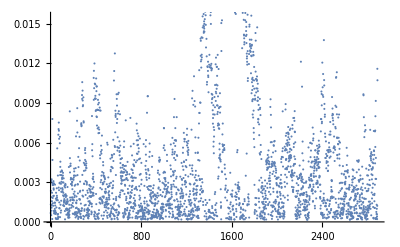

```mathematica
out3GBN[[1;;100]]
out3GBN[[1800;;1900]]
out4GBN;
Map[(#[[1]]-#[[9]])&,out3GBN]
ListPlot[Map[(#[[1]]-#[[9]])&,out4GBN]]
```